```mathematica
Exit[]
```

# Plots

## Plot Style

```mathematica
<<MaTeX`;
```

### Plot style

#### Colors

```mathematica
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
```

#### Dashing

```mathematica
dashed=Dashing[{0.025,0.02}];
dotted=Dashing[{0,0.02}];
dotdashed=Dashing[{0.015,0.02,0,0.02}];
```

#### Font magnification

```mathematica
magt=1.75;
magl=1.9;
```

#### Frame thickness

```mathematica
SetOptions[Plot,FrameStyle->Thickness[0.002]]
```

{AlignmentPoint→Center,AspectRatio→1/ϕ,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→Thickness[0.002],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

#### Ticks

```mathematica
bigl={0.025,0};
smalll={0.0125,0};

wtick[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[ToString[N[x]]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wtickint[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[ToString[x]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wtick[xmin_,xmax_,xbig_,xsmall_,padn_,padf_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[PaddedForm[x,{padn,padf}],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

wticknn[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x," ",bigl},{x," ",smalll}]],{i,0,xbig xsmall}];

Logwtick[xmin_,xmax_,xbig_,xsmall_]:=Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x,Style[""MaTeX[Superscript[10,Round[Log10[x]]]],Magnification->magt],bigl},{x," ",smalll}]],{i,0,xbig xsmall}];


Logwticknn[xmin_,xmax_,xbig_,xsmall_]:=
Table[Module[{x=xmin+(xmax-xmin)/(xbig xsmall) i},
If [Mod[i,xsmall]==0,{x," ",bigl},{x," ",smalll}]],{i,0,xbig xsmall}];
```

#### Legend

```mathematica
boxsize=0.1;
boxratio=4/3;
cutedge=0.02;
legbox[x_,y_,col_,fill_,boxt_,xmin_,xmax_,ymin_,ymax_]:=
{{fill,Rectangle[{x,y},{x+boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio}]},Join[col,{Line[{{x+cutedge boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2},{x+(1-cutedge)boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2}}]}],Text[Style[boxt,Magnification->magl],{x+1.2 boxsize(xmax-xmin),y+boxsize(ymax-ymin)/boxratio/2},{-1,0}]}

textbox[x_,y_,boxt_,xmin_,xmax_,ymin_,ymax_]:=
{Text[Style[boxt,FontFamily->Times,Magnification->magl],{x,y},{-1,0}]}
```

```mathematica
legdata[x_,y_,sc_]:={Rectangle[Offset[{-3sc,-3sc},{x,y}],Offset[{3sc,3sc},{x,y}]],
Line[{Offset[{0,-8sc},{x,y}],Offset[{0,8sc},{x,y}]}],
Line[{Offset[{-1.5sc,-8sc},{x,y}],Offset[{1.5sc,-8sc},{x,y}]}],
Line[{Offset[{-1.5sc,8sc},{x,y}],Offset[{1.5sc,8sc},{x,y}]}]};
```

## Plots

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
epJ0p25=Import["./datafiles/ep/J0p25.txt","Data","FieldSeparators"->","];
epJ0p5=Import["./datafiles/ep/J0p5.txt","Data","FieldSeparators"->","];
epJ1=Import["./datafiles/ep/J1.txt","Data","FieldSeparators"->","];
epJ1p5=Import["./datafiles/ep/J1p5.txt","Data","FieldSeparators"->","];

eCJ0p25=Import["./datafiles/eC/J0p25.txt","Data","FieldSeparators"->","];
eCJ0p5=Import["./datafiles/eC/J0p5.txt","Data","FieldSeparators"->","];
eCJ1=Import["./datafiles/eC/J1.txt","Data","FieldSeparators"->","];
eCJ1p5=Import["./datafiles/eC/J1p5.txt","Data","FieldSeparators"->","];

eAuJ0p25=Import["./datafiles/eAu/J0p25.txt","Data","FieldSeparators"->","];
eAuJ0p5=Import["./datafiles/eAu/J0p5.txt","Data","FieldSeparators"->","];
eAuJ1=Import["./datafiles/eAu/J1.txt","Data","FieldSeparators"->","];
eAuJ1p5=Import["./datafiles/eAu/J1p5.txt","Data","FieldSeparators"->","];

eAuJ0p25colonly=Import["./datafiles/eAu_collisionalonly/J0p25.txt","Data","FieldSeparators"->","];
eAuJ0p5colonly=Import["./datafiles/eAu_collisionalonly/J0p5.txt","Data","FieldSeparators"->","];
eAuJ1colonly=Import["./datafiles/eAu_collisionalonly/J1.txt","Data","FieldSeparators"->","];
eAuJ1p5colonly=Import["./datafiles/eAu_collisionalonly/J1p5.txt","Data","FieldSeparators"->","];

eUJ0p25=Import["./datafiles/eU/J0p25.txt","Data","FieldSeparators"->","];
eUJ0p5=Import["./datafiles/eU/J0p5.txt","Data","FieldSeparators"->","];
eUJ1=Import["./datafiles/eU/J1.txt","Data","FieldSeparators"->","];
eUJ1p5=Import["./datafiles/eU/J1p5.txt","Data","FieldSeparators"->","];
```

```mathematica
(*(eAuJ1p5t[[1]][[3]])/(eUJ1p5t[[1]][[3]])*)
```

0.196138

```mathematica
(*(eUJ0p25t[[1]][[3]])/(epJ0p25t[[1]][[3]])*)
```

5.04554

```mathematica
(*(eUJ1p5t[[1]][[3]])/(epJ1p5t[[1]][[3]])*)
```

3.95389

```mathematica
(*(eUJ0p25t[[1]][[3]])/(eUJ1p5t[[1]][[3]])*)
```

2117.32

```mathematica
Length[eAuJ0p25]
```

5000

```mathematica
Length[eAuJ0p25colonly]
```

5000

```mathematica
eAuJ0p5[[4900]]
eAuJ0p5colonly[[4900]]
```

{0.761797,0.139933,0.95,0.1,1.49226,0.15708,62330.5,43.7546}

{0.761797,0.139933,0.95,0.1,1.49226,0.15708,63304.8,44.0301}

```mathematica
62/63//N
```

0.984127

```mathematica
eAuJ0p5colonly[[4901]][[1]]
```

0.915882

```mathematica
eAuJ0p25cvsfull=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ0p25tcolonly,eAuJ0p25t}];
```

```mathematica
eAuJ0p25t=Select[eAuJ0p25,#[[1]]==eAuJ0p5[[4901]][[1]] &][[;;,{3,5,7}]];
eAuJ0p25tcolonly=Select[eAuJ0p25colonly,#[[1]]==eAuJ0p5colonly[[4901]][[1]] &][[;;,{3,5,7}]];

eAuJ0p5t=Select[eAuJ0p5,#[[1]]==eAuJ0p5[[4901]][[1]] &][[;;,{3,5,7}]];
eAuJ0p5tcolonly=Select[eAuJ0p5colonly,#[[1]]==eAuJ0p5colonly[[4901]][[1]] &][[;;,{3,5,7}]];

eAuJ1t=Select[eAuJ1,#[[1]]==eAuJ1[[4901]][[1]] &][[;;,{3,5,7}]];
eAuJ1tcolonly=Select[eAuJ1colonly,#[[1]]==eAuJ1colonly[[4901]][[1]] &][[;;,{3,5,7}]];

eAuJ1p5t=Select[eAuJ1p5,#[[1]]==eAuJ1p5[[4901]][[1]] &][[;;,{3,5,7}]];
eAuJ1p5tcolonly=Select[eAuJ1p5colonly,#[[1]]==eAuJ1p5colonly[[4901]][[1]] &][[;;,{3,5,7}]];
```

```mathematica
eAuJ0p25t=Select[eAuJ0p25,#[[1]]==eAuJ0p5[[4901]][[1]] &][[;;,{3,5,7}]];
eAuJ0p25tcolonly=Select[eAuJ0p25colonly,#[[1]]==eAuJ0p5colonly[[4901]][[1]] &][[;;,{3,5,7}]];
```

```mathematica
eAuJ0p25cvsfull=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ0p25tcolonly,eAuJ0p25t}];
eAuJ0p5cvsfull=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ0p5tcolonly,eAuJ0p5t}];
eAuJ1cvsfull=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ1tcolonly,eAuJ1t}];
eAuJ1p5cvsfull=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ1p5tcolonly,eAuJ1p5t}];
```

```mathematica
ListPlot3D[{eAuJ0p5cvsfull}]
```

-Graphics3D-

```mathematica
2/3//N
```

0.666667

```mathematica
ListPlot3D[{eAuJ0p25cvsfull}]
```

-Graphics3D-

```mathematica
epJ0p25t=Select[epJ0p25,#[[1]]==epJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
epJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ0p25t[[1]][[3]])}&,epJ0p25t];

eAuJ0p25t=Select[eAuJ0p25,#[[1]]==eAuJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eAuJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ0p25t[[1]][[3]])}&,eAuJ0p25t];

eCJ0p25t=Select[eCJ0p25,#[[1]]==eCJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eCJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ0p25t[[1]][[3]])}&,eCJ0p25t];


eUJ0p25t=Select[eUJ0p25,#[[1]]==eUJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eUJ0p25tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ0p25t[[1]][[3]])}&,eUJ0p25t];

epJ0p5t=Select[epJ0p5,#[[1]]==epJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
epJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ0p5t[[1]][[3]])}&,epJ0p5t];

eAuJ0p5t=Select[eAuJ0p5,#[[1]]==eAuJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eAuJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ0p5t[[1]][[3]])}&,eAuJ0p5t];

eUJ0p5t=Select[eUJ0p5,#[[1]]==eUJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eUJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ0p5t[[1]][[3]])}&,eUJ0p5t];

epJ1p5t=Select[epJ1p5,#[[1]]==epJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
epJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ1p5t[[1]][[3]])}&,epJ1p5t];

eAuJ1p5t=Select[eAuJ1p5,#[[1]]==eAuJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eAuJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ1p5t[[1]][[3]])}&,eAuJ1p5t];

eUJ1p5t=Select[eUJ1p5,#[[1]]==eUJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eUJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ1p5t[[1]][[3]])}&,eUJ1p5t];

epJ1t=Select[epJ1,#[[1]]==epJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
epJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(epJ1t[[1]][[3]])}&,epJ1t];

eAuJ1t=Select[eAuJ1,#[[1]]==eAuJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eAuJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eAuJ1t[[1]][[3]])}&,eAuJ1t];

eUJ1t=Select[eUJ1,#[[1]]==eUJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eUJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eUJ1t[[1]][[3]])}&,eUJ1t];


eCJ0p5t=Select[eCJ0p5,#[[1]]==eCJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eCJ0p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ0p5t[[1]][[3]])}&,eCJ0p5t];
eCJ1p5t=Select[eCJ1p5,#[[1]]==eCJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eCJ1p5tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ1p5t[[1]][[3]])}&,eCJ1p5t];
eCJ1t=Select[eCJ1,#[[1]]==eCJ0p5[[19901]][[1]] &][[;;,{3,5,7}]];
eCJ1tt=Map[{#[[1]],#[[2]],(#[[3]])/(eCJ1t[[1]][[3]])}&,eCJ1t];


eCJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25t[[1]][[3]])/(eCJ0p25t[[1]][[3]])}&,{eCJ0p25t,epJ0p25t}];
eCJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5t[[1]][[3]])/(eCJ0p5t[[1]][[3]])}&,{eCJ0p5t,epJ0p5t}];
eCJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5t[[1]][[3]])/(eCJ1p5t[[1]][[3]])}&,{eCJ1p5t,epJ1p5t}];
eCJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1t[[1]][[3]])/(eCJ1t[[1]][[3]])}&,{eCJ1t,epJ1t}];
eAuJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25t[[1]][[3]])/(eAuJ0p25t[[1]][[3]])}&,{eAuJ0p25t,epJ0p25t}];

eUJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25t[[1]][[3]])/(eUJ0p25t[[1]][[3]])}&,{eUJ0p25t,epJ0p25t}];
eAuJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5t[[1]][[3]])/(eAuJ0p5t[[1]][[3]])}&,{eAuJ0p5t,epJ0p5t}];

eUJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5t[[1]][[3]])/(eUJ0p5t[[1]][[3]])}&,{eUJ0p5t,epJ0p5t}];

eAuJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5t[[1]][[3]])/(eAuJ1p5t[[1]][[3]])}&,{eAuJ1p5t,epJ1p5t}];

eUJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5t[[1]][[3]])/(eUJ1p5t[[1]][[3]])}&,{eUJ1p5t,epJ1p5t}];

eAuJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1t[[1]][[3]])/(eAuJ1t[[1]][[3]])}&,{eAuJ1t,epJ1t}];

eUJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1t[[1]][[3]])/(eUJ1t[[1]][[3]])}&,{eUJ1t,epJ1t}];

(*
epJ0p5t=Select[epJ0p5,#[[1]]==epJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
epJ1t=Select[epJ1,#[[1]]==epJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
epJ1p5t=Select[epJ1p5,#[[1]]==epJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];

eAuJ0p25t=Select[eAuJ0p25,#[[1]]==eAuJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eAuJ0p5t=Select[eAuJ0p5,#[[1]]==eAuJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eAuJ1t=Select[eAuJ1,#[[1]]==eAuJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eAuJ1p5t=Select[eAuJ1p5,#[[1]]==eAuJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];

eUJ0p25t=Select[eUJ0p25,#[[1]]==eUJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eUJ0p5t=Select[eUJ0p5,#[[1]]==eUJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eUJ1t=Select[eUJ1,#[[1]]==eUJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];
eUJ1p5t=Select[eUJ1p5,#[[1]]==eUJ0p5[[19001]][[1]] &][[;;,{3,5,7}]];*)
```

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 19901 of {{0.000110113,0.0000202264,0.05,0.1,0.0785398,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.235619,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.392699,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.549779,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.706858,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,0.863938,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.02102,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.1781,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.33518,0.15708,0,0},{0.000110113,0.0000202264,0.05,0.1,1.49226,0.15708,0,0},«4990»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ0p25t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,8752.08},{0.025,0.11781,8962.16},{0.025,0.19635,9070.3},{0.025,0.274889,9121.34},{0.025,0.353429,9055.98},{0.025,0.431969,8865.83},{0.025,0.510509,8917.01},{0.025,0.589049,9096.29},{0.025,0.667588,9051.23},{0.025,0.746128,8938.87},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ0p5t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,1727.46},{0.025,0.11781,1754.42},{0.025,0.19635,1783.55},{0.025,0.274889,1807.79},{0.025,0.353429,1780.93},{0.025,0.431969,1742.96},{0.025,0.510509,1755.98},{0.025,0.589049,1795.82},{0.025,0.667588,1771.33},{0.025,0.746128,1761},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ1p5t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,4.75996},{0.025,0.11781,4.72181},{0.025,0.19635,4.96361},{0.025,0.274889,5.09385},{0.025,0.353429,4.73545},{0.025,0.431969,4.75113},{0.025,0.510509,4.75167},{0.025,0.589049,4.86937},{0.025,0.667588,4.65546},{0.025,0.746128,4.71321},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ1t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,80.4313},{0.025,0.11781,80.8351},{0.025,0.19635,83.3983},{0.025,0.274889,85.5709},{0.025,0.353429,81.7536},{0.025,0.431969,80.8456},{0.025,0.510509,81.5064},{0.025,0.589049,83.5219},{0.025,0.667588,81.0119},{0.025,0.746128,81.0298},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ0p25t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,8419.14},{0.025,0.11781,8500.53},{0.025,0.19635,8620.97},{0.025,0.274889,8390.07},{0.025,0.353429,8424.74},{0.025,0.431969,8474.98},{0.025,0.510509,8473.4},{0.025,0.589049,8627.58},{0.025,0.667588,8658.64},{0.025,0.746128,8492.87},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ0p5t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,1427.76},{0.025,0.11781,1452.07},{0.025,0.19635,1475.39},{0.025,0.274889,1422.35},{0.025,0.353429,1435.18},{0.025,0.431969,1443.38},{0.025,0.510509,1441.43},{0.025,0.589049,1466.48},{0.025,0.667588,1478.91},{0.025,0.746128,1440.83},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ1p5t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,3.97631},{0.025,0.11781,4.10257},{0.025,0.19635,4.1309},{0.025,0.274889,3.94692},{0.025,0.353429,3.98789},{0.025,0.431969,3.9679},{0.025,0.510509,4.11935},{0.025,0.589049,4.15208},{0.025,0.667588,4.10833},{0.025,0.746128,3.97647},«390»},{}}]; dimensions are 400 and 0.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1⟦1⟧,#1⟦2⟧,(#1⟦3⟧ epJ1t⟦1⟧⟦3⟧)/(Slot[«1»]⟦3⟧ Part[«2»]⟦3⟧)}&,{{{0.025,0.0392699,22.3751},{0.025,0.11781,22.7001},{0.025,0.19635,23.0941},{0.025,0.274889,21.9745},{0.025,0.353429,22.6503},{0.025,0.431969,23.0958},{0.025,0.510509,21.8379},{0.025,0.589049,23.9806},{0.025,0.667588,23.4204},{0.025,0.746128,22.6065},«390»},{}}]; dimensions are 400 and 0.

```mathematica
ListPlot3D[{eCJ0p25ratio,eUJ0p25ratio},PlotRange->{0.9,2}]
ListPlot3D[{eCJ0p5ratio,eUJ0p5ratio},PlotRange->{0.9,2}]
ListPlot3D[{eCJ1ratio,eUJ1ratio},PlotRange->{0.9,2}]
ListPlot3D[{eCJ1p5ratio,eUJ1p5ratio},PlotRange->{0.9,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ListPlot3D[{eAuJ0p25ratio,eCJ0p25ratio,eUJ0p25ratio},PlotRange->{0.9,2}]
ListPlot3D[{eAuJ0p5ratio,eCJ0p5ratio,eUJ0p5ratio},PlotRange->{0.9,2}]
ListPlot3D[{eAuJ1ratio,eCJ1ratio,eUJ1ratio},PlotRange->{0.9,2}]
ListPlot3D[{eAuJ1p5ratio,eCJ1p5ratio,eUJ1p5ratio},PlotRange->{0.9,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ListPlot3D[e1p5ratio]
```

-Graphics3D-

```mathematica
ListPlot3D[{e0p25ratio,e1p5ratio}]
```

-Graphics3D-

```mathematica
e0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ0p25ratio,eUJ0p25ratio}];
e1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])}&,{eAuJ1p5ratio,eUJ1p5ratio}];

eUJ0p25ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p25t[[1]][[3]])/(eUJ0p25t[[1]][[3]])}&,{eUJ0p25t,epJ0p25t}];
eAuJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5t[[1]][[3]])/(eAuJ0p5t[[1]][[3]])}&,{eAuJ0p5t,epJ0p5t}];

eUJ0p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ0p5t[[1]][[3]])/(eUJ0p5t[[1]][[3]])}&,{eUJ0p5t,epJ0p5t}];

eAuJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5t[[1]][[3]])/(eAuJ1p5t[[1]][[3]])}&,{eAuJ1p5t,epJ1p5t}];

eUJ1p5ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1p5t[[1]][[3]])/(eUJ1p5t[[1]][[3]])}&,{eUJ1p5t,epJ1p5t}];

eAuJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1t[[1]][[3]])/(eAuJ1t[[1]][[3]])}&,{eAuJ1t,epJ1t}];

eUJ1ratio=MapThread[{#1[[1]],#1[[2]],(#1[[3]])/(#2[[3]])(epJ1t[[1]][[3]])/(eUJ1t[[1]][[3]])}&,{eUJ1t,epJ1t}];
```

```mathematica
ListPlot3D[eAuJ0p25ratio]
```

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- ({})

ListPlot3D[{}]

```mathematica
ListPlot3D[{eAuJ0p25ratio,eAuJ1ratio,eAuJ1p5ratio},PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{eAuJ0p25tt,eUJ0p25tt},PlotStyle->Opacity[0.75]]
ListPlot3D[{eAuJ1p5tt,eUJ1p5tt},PlotStyle->Opacity[0.75]]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D[{epJ0p25tt,eCJ0p25tt,eAuJ0p25tt,eUJ0p25tt},PlotStyle->Opacity[0.75],PlotRange->{0,15}]
ListPlot3D[{epJ0p5tt,eCJ0p5tt,eAuJ0p5tt,eUJ0p5tt},PlotStyle->Opacity[0.75],PlotRange->{0,15}]
ListPlot3D[{epJ1tt,eCJ1tt,eAuJ1tt,eUJ1tt},PlotStyle->Opacity[0.75],PlotRange->{0,15}]
ListPlot3D[{epJ1p5tt,eCJ1p5tt,eAuJ1p5tt,eUJ1p5tt},PlotStyle->Opacity[0.75],PlotRange->{0,15}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
epJ0p5[[1]][[1]]
```

0.000110113

```mathematica
fig2=Import["./datafiles/fig2.dat","Data","FieldSeparators"->","];
fig3=Import["./datafiles/fig3.dat","Data","FieldSeparators"->","];
fig3ReA=Import["./datafiles/fig3_ReA.dat","Data","FieldSeparators"->","];
fig4=Import["./datafiles/fig4.dat","Data","FieldSeparators"->","];
fig5=Import["./datafiles/fig5.dat","Data","FieldSeparators"->","];
fig5ReA=Import["./datafiles/fig5_ReA.dat","Data","FieldSeparators"->","];
(*fig5insert=Import["./datafiles/fig5_insert_isospin.dat","Data","FieldSeparators"->","];*)
fig5insert=Import["./datafiles/fig5_insert.dat","Data","FieldSeparators"->","];
qhatxQ=Import["./datafiles/qhat_data_Au.dat","Data","FieldSeparators"->","];
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
Alist=Table[10^(fig5insert[[i]][[1]]),{i,1,Length[fig5insert]}];
```

```mathematica
fig2[[i]][[1]]-(fig2[[i]][[2]])/2
```

Part::pkspec1: The expression i cannot be used as a part specification.

{{0.000110113-i/2,0.0000202264-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000132385-i/2,0.0000243175-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000159162-i/2,0.0000292361-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000191355-i/2,0.0000351495-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000230059-i/2,0.000042259-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000276592-i/2,0.0000508065-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000332537-i/2,0.0000610829-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000399797-i/2,0.0000734378-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000480662-i/2,0.0000882916-i/2,3.13838×10^-6-i/2,2.21917×10^-6-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000577882-i/2,0.00010615-i/2,-i/2,-i/2,-i/2,-i/2,2.61581×10^-6-i/2,1.84966×10^-6-i/2,2.07605×10^-6-i/2,1.46799×10^-6-i/2},{0.000694767-i/2,0.00012762-i/2,5.04706×10^-6-i/2,2.59128×10^-6-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.000835294-i/2,0.000153433-i/2,0.0000112335-i/2,4.7355×10^-6-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.00100424-i/2,0.000184467-i/2,7.02016×10^-6-i/2,4.964×10^-6-i/2,0.0000120781-i/2,6.47236×10^-6-i/2,-i/2,-i/2,2.39045×10^-6-i/2,1.6903×10^-6-i/2},{0.00120737-i/2,0.000221779-i/2,3.12299×10^-6-i/2,2.20829×10^-6-i/2,-i/2,-i/2,-i/2,-i/2,-i/2,-i/2},{0.00145157-i/2,0.000266636-i/2,0.0000158378-i/2,4.93979×10^-6-i/2,0.0000305095-i/2,0.0000153261-i/2,0.0000104776-i/2,7.40878×10^-6-i/2,8.35832×10^-6-i/2,5.91023×10^-6-i/2},{0.00174518-i/2,0.000320568-i/2,0.000024361-i/2,7.84061×10^-6-i/2,7.3724×10^-6-i/2,5.21307×10^-6-i/2,0.0000147056-i/2,0.0000103984-i/2,0.0000100379-i/2,5.05613×10^-6-i/2},{0.00209816-i/2,0.000385407-i/2,0.0000204337-i/2,8.13263×10^-6-i/2,-i/2,-i/2,0.0000209499-i/2,0.000010978-i/2,0.0000503028-i/2,0.0000193774-i/2},{0.00252255-i/2,0.000463361-i/2,0.0000255077-i/2,6.54631×10^-6-i/2,7.27578×10^-6-i/2,5.14476×10^-6-i/2,0.0000579348-i/2,0.0000181931-i/2,5.80833×10^-6-i/2,4.10711×10^-6-i/2},{0.00303277-i/2,0.000557083-i/2,0.0000582701-i/2,0.0000117633-i/2,0.0000259692-i/2,0.0000130816-i/2,0.0000546429-i/2,0.000017388-i/2,0.00002221-i/2,9.10965×10^-6-i/2},{0.00364619-i/2,0.00066976-i/2,0.0000768955-i/2,0.0000122009-i/2,0.0000818782-i/2,0.0000195749-i/2,0.0000728317-i/2,0.0000207439-i/2,0.0000847724-i/2,0.0000222616-i/2},{0.00438369-i/2,0.000805229-i/2,0.0000637916-i/2,0.0000121016-i/2,0.0000900968-i/2,0.0000301986-i/2,0.000114987-i/2,0.0000281741-i/2,0.0000941125-i/2,0.0000190266-i/2},{0.00527035-i/2,0.000968098-i/2,0.000114128-i/2,0.0000162224-i/2,0.000141958-i/2,0.0000329395-i/2,0.000103001-i/2,0.0000218215-i/2,0.0000450632-i/2,0.0000123688-i/2},{0.00633635-i/2,0.00116391-i/2,0.000195217-i/2,0.0000212238-i/2,0.000110483-i/2,0.0000236288-i/2,0.000226578-i/2,0.0000340339-i/2,0.00017791-i/2,0.000030939-i/2},{0.00761797-i/2,0.00139933-i/2,0.000256224-i/2,0.0000247433-i/2,0.000263097-i/2,0.000042696-i/2,0.000212629-i/2,0.0000357697-i/2,0.000308476-i/2,0.0000383247-i/2},{0.00915882-i/2,0.00168236-i/2,0.00037392-i/2,0.0000290217-i/2,0.00033926-i/2,0.000046968-i/2,0.00020403-i/2,0.0000367784-i/2,0.000406695-i/2,0.000047347-i/2},{0.0110113-i/2,0.00202264-i/2,0.000550999-i/2,0.0000360355-i/2,0.000468989-i/2,0.0000488783-i/2,0.000578126-i/2,0.0000570663-i/2,0.000496524-i/2,0.0000495242-i/2},{0.0132385-i/2,0.00243175-i/2,0.000769988-i/2,0.0000419491-i/2,0.000895364-i/2,0.0000769722-i/2,0.000756378-i/2,0.0000635582-i/2,0.000692521-i/2,0.000059842-i/2},{0.0159162-i/2,0.00292361-i/2,0.00117302-i/2,0.0000504966-i/2,0.00101044-i/2,0.000080638-i/2,0.00105612-i/2,0.0000777459-i/2,0.00130563-i/2,0.0000842553-i/2},{0.0191355-i/2,0.00351495-i/2,0.00150784-i/2,0.0000579662-i/2,0.00163151-i/2,0.000105445-i/2,0.00161968-i/2,0.0000958778-i/2,0.00160192-i/2,0.0000904318-i/2},{0.0230059-i/2,0.0042259-i/2,0.00237813-i/2,0.0000730838-i/2,0.00188789-i/2,0.000113638-i/2,0.00228848-i/2,0.000115438-i/2,0.00237915-i/2,0.000110673-i/2},{0.0276592-i/2,0.00508065-i/2,0.00358167-i/2,0.000089594-i/2,0.0031573-i/2,0.000146093-i/2,0.00361966-i/2,0.000148944-i/2,0.00329624-i/2,0.000128907-i/2},{0.0332537-i/2,0.00610829-i/2,0.00506219-i/2,0.000106843-i/2,0.00504927-i/2,0.000182637-i/2,0.00474559-i/2,0.000166763-i/2,0.00514639-i/2,0.00016398-i/2},{0.0399797-i/2,0.00734378-i/2,0.00691907-i/2,0.00012132-i/2,0.0073804-i/2,0.000224708-i/2,0.00713992-i/2,0.000205904-i/2,0.0071707-i/2,0.000191191-i/2},{0.0480662-i/2,0.00882916-i/2,0.00988411-i/2,0.000147442-i/2,0.0095487-i/2,0.000250139-i/2,0.00955611-i/2,0.000238717-i/2,0.00973278-i/2,0.000223185-i/2},{0.0577882-i/2,0.010615-i/2,0.014474-i/2,0.00017798-i/2,0.0146517-i/2,0.000313325-i/2,0.0140865-i/2,0.000289588-i/2,0.0147698-i/2,0.000276659-i/2},{0.0694767-i/2,0.012762-i/2,0.0202778-i/2,0.000209873-i/2,0.0197945-i/2,0.000359533-i/2,0.0203029-i/2,0.000347841-i/2,0.0193717-i/2,0.000307331-i/2},{0.0835294-i/2,0.0153433-i/2,0.027212-i/2,0.000241893-i/2,0.0284395-i/2,0.000431726-i/2,0.0281833-i/2,0.000401594-i/2,0.0278461-i/2,0.00037001-i/2},{0.100424-i/2,0.0184467-i/2,0.0362587-i/2,0.00027392-i/2,0.0361645-i/2,0.000468352-i/2,0.0371149-i/2,0.000456355-i/2,0.0368391-i/2,0.000417498-i/2},{0.120737-i/2,0.0221779-i/2,0.0461733-i/2,0.000301052-i/2,0.048243-i/2,0.000532549-i/2,0.0459411-i/2,0.000486065-i/2,0.0470611-i/2,0.00045805-i/2},{0.145157-i/2,0.0266636-i/2,0.057145-i/2,0.000326979-i/2,0.0570955-i/2,0.00055406-i/2,0.056438-i/2,0.000519991-i/2,0.0568531-i/2,0.000485228-i/2},{0.174518-i/2,0.0320568-i/2,0.0674885-i/2,0.000344077-i/2,0.0665205-i/2,0.000573603-i/2,0.0675232-i/2,0.000545098-i/2,0.068686-i/2,0.000508638-i/2},{0.209816-i/2,0.0385407-i/2,0.0748747-i/2,0.000346501-i/2,0.0767177-i/2,0.000589364-i/2,0.0769904-i/2,0.000557318-i/2,0.0797395-i/2,0.000522865-i/2},{0.252255-i/2,0.0463361-i/2,0.0812657-i/2,0.000345459-i/2,0.0864292-i/2,0.000594569-i/2,0.0856453-i/2,0.000558594-i/2,0.0917237-i/2,0.000535727-i/2},{0.303277-i/2,0.0557083-i/2,0.0855831-i/2,0.000338845-i/2,0.0944692-i/2,0.000589456-i/2,0.0958945-i/2,0.000561307-i/2,0.098594-i/2,0.000525114-i/2},{0.364619-i/2,0.066976-i/2,0.0867613-i/2,0.000326981-i/2,0.101597-i/2,0.00058288-i/2,0.106119-i/2,0.00056553-i/2,0.109808-i/2,0.00052959-i/2},{0.438369-i/2,0.0805229-i/2,0.08613-i/2,0.000313389-i/2,0.110125-i/2,0.000582511-i/2,0.113595-i/2,0.000561494-i/2,0.120258-i/2,0.000535535-i/2},{0.527035-i/2,0.0968098-i/2,0.0821293-i/2,0.000295931-i/2,0.118057-i/2,0.00058094-i/2,0.118382-i/2,0.000552681-i/2,0.130205-i/2,0.000536798-i/2},{0.633635-i/2,0.116391-i/2,0.0765608-i/2,0.00027829-i/2,0.123708-i/2,0.000579829-i/2,0.126735-i/2,0.000555304-i/2,0.13608-i/2,0.000536025-i/2},{0.761797-i/2,0.139933-i/2,0.0684847-i/2,0.000257788-i/2,0.126554-i/2,0.000577243-i/2,0.127013-i/2,0.000545364-i/2,0.139983-i/2,0.00053311-i/2},{0.915882-i/2,0.168236-i/2,0.0560999-i/2,0.000231197-i/2,0.119112-i/2,0.000550637-i/2,0.119957-i/2,0.000522615-i/2,0.132844-i/2,0.000515758-i/2}}

```mathematica
fig2[[i]][[2]]
```

```mathematica
fig2[[i]][[1]]-(fig2[[i]][[2]])/2
```

```mathematica
f2tb[n_]:=Join[Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[2]])},{i,1,Length[fig2]}],{{fig2[[Length[fig2]]][[1]]+(fig2[[Length[fig2]]][[2]])/2,(fig2[[Length[fig2]]][[2n+1]])/(fig2[[]][[2]])}}]
f3tb[n_]:=Join[Table[{fig3[[i]][[1]]-(fig3[[i]][[2]])/2,fig3[[i]][[2n+1]]},{i,1,Length[fig3]}],{{fig3[[Length[fig3]]][[1]]+(fig3[[Length[fig3]]][[2]])/2,fig3[[Length[fig3]]][[2n+1]]}}]
f3ReAtb[n_]:=Join[Table[{fig3ReA[[i]][[1]]-(fig3ReA[[i]][[2]])/2,fig3ReA[[i]][[2n+1]]},{i,1,Length[fig3ReA]}],{{fig3ReA[[Length[fig3ReA]]][[1]]+(fig3ReA[[Length[fig3ReA]]][[2]])/2,fig3ReA[[Length[fig3ReA]]][[2n+1]]}}]
f4tb[n_]:=Join[Table[{fig4[[i]][[1]]-(fig4[[i]][[2]])/2,fig4[[i]][[2n+1]]},{i,1,Length[fig4]}],{{fig4[[Length[fig4]]][[1]]+(fig4[[Length[fig4]]][[2]])/2,fig4[[Length[fig4]]][[2n+1]]}}]
f5tb[n_]:=Join[Table[{Alist[[n]]^(1/6)(fig5[[i]][[1]]-(fig5[[i]][[2]])/2),fig5[[i]][[2n+1]]},{i,1,Length[fig5]}],{{Alist[[n]]^(1/6)(fig5[[Length[fig5]]][[1]]+(fig5[[Length[fig5]]][[2]])/2),fig5[[Length[fig5]]][[2n+1]]}}]
f5ReAtb[n_]:=Join[Table[{Alist[[n]]^(1/6)(fig5ReA[[i]][[1]]-(fig5ReA[[i]][[2]])/2),fig5ReA[[i]][[2n+1]]},{i,1,Length[fig5ReA]}],{{Alist[[n]]^(1/6)(fig5ReA[[Length[fig5ReA]]][[1]]+(fig5ReA[[Length[fig5ReA]]][[2]])/2),fig5ReA[[Length[fig5ReA]]][[2n+1]]}}]
```

```mathematica
f2tberr[n_]:=Table[{fig2[[i]][[1]],(fig2[[i]][[2n+1]])/(fig2[[i]][[2]])±(fig2[[i]][[2n+2]])/(fig2[[i]][[2]])},{i,1,Length[fig2]}]
f3tberr[n_]:=Table[{fig3[[i]][[1]],fig3[[i]][[2n+1]]±fig3[[i]][[2n+2]]},{i,1,Length[fig3]}]
f4tberr[n_]:=Table[{fig4[[i]][[1]],fig4[[i]][[2n+1]]±fig4[[i]][[2n+2]]},{i,1,Length[fig4]}]
f5tberr[n_]:=Table[{Alist[[n]]^(1/6)fig5[[i]][[1]],fig5[[i]][[2n+1]]±fig5[[i]][[2n+2]]},{i,1,Length[fig5]}]
f3ReAtberr[n_]:=Table[{fig3ReA[[i]][[1]],fig3ReA[[i]][[2n+1]]±fig3ReA[[i]][[2n+2]]},{i,1,Length[fig3ReA]}]
f5ReAtberr[n_]:=Table[{Alist[[n]]^(1/6)fig5ReA[[i]][[1]],fig5ReA[[i]][[2n+1]]±fig5ReA[[i]][[2n+2]]},{i,1,Length[fig5ReA]}]
```

```mathematica
f2tberr[1]
```

(0.000110113 | 0.±0.
0.000132385 | 0.±0.
0.000159162 | 0.±0.
0.000191355 | 0.±0.
0.000230059 | 0.±0.
0.000276592 | 0.±0.
0.000332537 | 0.±0.
0.000399797 | 0.±0.
0.000480662 | 0.0355456±0.0251346
0.000577882 | 0.±0.
0.000694767 | 0.0395476±0.0203047
0.000835294 | 0.0732144±0.0308636
0.00100424 | 0.0380565±0.02691
0.00120737 | 0.0140815±0.00995716
0.00145157 | 0.0593986±0.0185263
0.00174518 | 0.0759932±0.0244585
0.00209816 | 0.0530185±0.0211014
0.00252255 | 0.0550493±0.0141279
0.00303277 | 0.104599±0.0211159
0.00364619 | 0.114811±0.0182168
0.00438369 | 0.0792217±0.0150288
0.00527035 | 0.117889±0.016757
0.00633635 | 0.167725±0.0182349
0.00761797 | 0.183105±0.0176822
0.00915882 | 0.222259±0.0172506
0.0110113 | 0.272416±0.0178161
0.0132385 | 0.316639±0.0172506
0.0159162 | 0.401223±0.017272
0.0191355 | 0.428979±0.0164913
0.0230059 | 0.562751±0.0172943
0.0276592 | 0.704963±0.0176344
0.0332537 | 0.828741±0.0174915
0.0399797 | 0.942167±0.0165201
0.0480662 | 1.11948±0.0166994
0.0577882 | 1.36354±0.0167668
0.0694767 | 1.58892±0.0164451
0.0835294 | 1.77354±0.0157654
0.100424 | 1.96559±0.0148493
0.120737 | 2.08195±0.0135744
0.145157 | 2.14318±0.0122631
0.174518 | 2.10528±0.0107334
0.209816 | 1.94274±0.00899052
0.252255 | 1.75383±0.0074555
0.303277 | 1.53627±0.00608249
0.364619 | 1.29541±0.00488206
0.438369 | 1.06963±0.00389192
0.527035 | 0.848357±0.00305683
0.633635 | 0.65779±0.00239099
0.761797 | 0.489411±0.00184222
0.915882 | 0.33346±0.00137424)

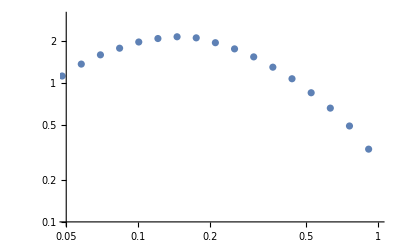

```mathematica
ListLogLogPlot[{f2tberr[1]},PlotRange->{{0.05,1},{1*10^-1,3}}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

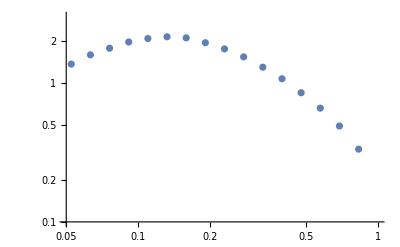

```mathematica
ListLogLogPlot[{f2tb[1]},PlotRange->{{0.05,1},{1*10^-1,3}}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

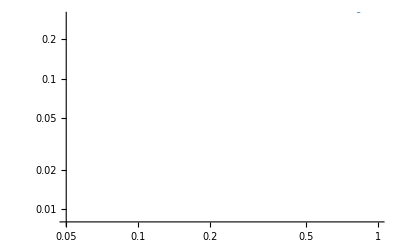

```mathematica
ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

```mathematica
baseline=Import["./datafiles/baseline_pT2030.dat","Data","FieldSeparators"->","];
baselinetb[n_]:=Join[Table[{baseline[[i]][[1]]-(baseline[[i]][[2]])/2,baseline[[i]][[2n+1]]},{i,1,Length[baseline]}],{{baseline[[Length[baseline]]][[1]]+(baseline[[Length[baseline]]][[2]])/2,baseline[[Length[baseline]]][[2n+1]]}}]
baselinetberr[n_]:=Table[{baseline[[i]][[1]],baseline[[i]][[2n+1]]±baseline[[i]][[2n+2]]},{i,1,Length[baseline]}]
```

Import::nffil: File ./datafiles/baseline_pT2030.dat not found during Import.

```mathematica
ListPlot[{baselinetb[1],baselinetb[2],baselinetb[3]},Joined->True]
```

Part::partd: Part specification Symbol⟦1⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦2⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
pTeta00=Import["./datafiles/raw_eec_0_0.dat","Data","FieldSeparators"->","];
pTeta01=Import["./datafiles/raw_eec_0_1.dat","Data","FieldSeparators"->","];
pTeta02=Import["./datafiles/raw_eec_0_2.dat","Data","FieldSeparators"->","];

pTeta10=Import["./datafiles/raw_eec_1_0.dat","Data","FieldSeparators"->","];
pTeta11=Import["./datafiles/raw_eec_1_1.dat","Data","FieldSeparators"->","];
pTeta12=Import["./datafiles/raw_eec_1_2.dat","Data","FieldSeparators"->","];

pTeta20=Import["./datafiles/raw_eec_2_0.dat","Data","FieldSeparators"->","];
pTeta21=Import["./datafiles/raw_eec_2_1.dat","Data","FieldSeparators"->","];
pTeta22=Import["./datafiles/raw_eec_2_2.dat","Data","FieldSeparators"->","];
```

```mathematica
pTeta00tb[n_]:=Join[Table[{pTeta00[[i]][[1]]-(pTeta00[[i]][[2]])/2,(pTeta00[[i]][[2n+1]])/(pTeta00[[i]][[2]])},{i,1,Length[pTeta00]}],{{pTeta00[[Length[pTeta00]]][[1]]+(pTeta00[[Length[pTeta00]]][[2]])/2,(pTeta00[[Length[pTeta00]]][[2n+1]])/(pTeta00[[Length[pTeta00]]][[2]])}}]
pTeta00tberr[n_]:=Table[{pTeta00[[i]][[1]],(pTeta00[[i]][[2n+1]])/(pTeta00[[i]][[2]])±(pTeta00[[i]][[2n+2]])/(pTeta00[[i]][[2]])},{i,1,Length[pTeta00]}]

pTeta01tb[n_]:=Join[Table[{pTeta01[[i]][[1]]-(pTeta01[[i]][[2]])/2,(pTeta01[[i]][[2n+1]])/(pTeta01[[i]][[2]])},{i,1,Length[pTeta01]}],{{pTeta01[[Length[pTeta01]]][[1]]+(pTeta01[[Length[pTeta01]]][[2]])/2,(pTeta01[[Length[pTeta01]]][[2n+1]])/(pTeta01[[Length[pTeta01]]][[2]])}}]
pTeta01tberr[n_]:=Table[{pTeta01[[i]][[1]],(pTeta01[[i]][[2n+1]])/(pTeta01[[i]][[2]])±(pTeta01[[i]][[2n+2]])/(pTeta01[[i]][[2]])},{i,1,Length[pTeta01]}]

pTeta02tb[n_]:=Join[Table[{pTeta02[[i]][[1]]-(pTeta02[[i]][[2]])/2,(pTeta02[[i]][[2n+1]])/(pTeta02[[i]][[2]])},{i,1,Length[pTeta02]}],{{pTeta02[[Length[pTeta02]]][[1]]+(pTeta02[[Length[pTeta02]]][[2]])/2,(pTeta02[[Length[pTeta02]]][[2n+1]])/(pTeta02[[Length[pTeta02]]][[2]])}}]
pTeta02tberr[n_]:=Table[{pTeta02[[i]][[1]],(pTeta02[[i]][[2n+1]])/(pTeta02[[i]][[2]])±(pTeta02[[i]][[2n+2]])/(pTeta02[[i]][[2]])},{i,1,Length[pTeta02]}]

pTeta10tb[n_]:=Join[Table[{pTeta10[[i]][[1]]-(pTeta10[[i]][[2]])/2,(pTeta10[[i]][[2n+1]])/(pTeta10[[i]][[2]])},{i,1,Length[pTeta10]}],{{pTeta10[[Length[pTeta10]]][[1]]+(pTeta10[[Length[pTeta10]]][[2]])/2,(pTeta10[[Length[pTeta10]]][[2n+1]])/(pTeta10[[Length[pTeta10]]][[2]])}}]
pTeta10tberr[n_]:=Table[{pTeta10[[i]][[1]],(pTeta10[[i]][[2n+1]])/(pTeta10[[i]][[2]])±(pTeta10[[i]][[2n+2]])/(pTeta10[[i]][[2]])},{i,1,Length[pTeta10]}]

pTeta11tb[n_]:=Join[Table[{pTeta11[[i]][[1]]-(pTeta11[[i]][[2]])/2,(pTeta11[[i]][[2n+1]])/(pTeta11[[i]][[2]])},{i,1,Length[pTeta11]}],{{pTeta11[[Length[pTeta11]]][[1]]+(pTeta11[[Length[pTeta11]]][[2]])/2,(pTeta11[[Length[pTeta11]]][[2n+1]])/(pTeta11[[Length[pTeta11]]][[2]])}}]
pTeta11tberr[n_]:=Table[{pTeta11[[i]][[1]],(pTeta11[[i]][[2n+1]])/(pTeta11[[i]][[2]])±(pTeta11[[i]][[2n+2]])/(pTeta11[[i]][[2]])},{i,1,Length[pTeta11]}]

pTeta12tb[n_]:=Join[Table[{pTeta12[[i]][[1]]-(pTeta12[[i]][[2]])/2,(pTeta12[[i]][[2n+1]])/(pTeta12[[i]][[2]])},{i,1,Length[pTeta12]}],{{pTeta12[[Length[pTeta12]]][[1]]+(pTeta12[[Length[pTeta12]]][[2]])/2,(pTeta12[[Length[pTeta12]]][[2n+1]])/(pTeta12[[Length[pTeta12]]][[2]])}}]
pTeta12tberr[n_]:=Table[{pTeta12[[i]][[1]],(pTeta12[[i]][[2n+1]])/(pTeta12[[i]][[2]])±(pTeta12[[i]][[2n+2]])/(pTeta12[[i]][[2]])},{i,1,Length[pTeta12]}]

pTeta20tb[n_]:=Join[Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[2]])},{i,1,Length[pTeta20]}],{{pTeta20[[Length[pTeta20]]][[1]]+(pTeta20[[Length[pTeta20]]][[2]])/2,(pTeta20[[Length[pTeta20]]][[2n+1]])/(pTeta20[[Length[pTeta20]]][[2]])}}]
pTeta20tberr[n_]:=Table[{pTeta20[[i]][[1]],(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[2]])±(pTeta20[[i]][[2n+2]])/(pTeta20[[i]][[2]])},{i,1,Length[pTeta20]}]

pTeta21tb[n_]:=Join[Table[{pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2,(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[2]])},{i,1,Length[pTeta21]}],{{pTeta21[[Length[pTeta21]]][[1]]+(pTeta21[[Length[pTeta21]]][[2]])/2,(pTeta21[[Length[pTeta21]]][[2n+1]])/(pTeta21[[Length[pTeta21]]][[2]])}}]
pTeta21tberr[n_]:=Table[{pTeta21[[i]][[1]],(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[2]])±(pTeta21[[i]][[2n+2]])/(pTeta21[[i]][[2]])},{i,1,Length[pTeta21]}]

pTeta22tb[n_]:=Join[Table[{pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2,(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[2]])},{i,1,Length[pTeta22]}],{{pTeta22[[Length[pTeta22]]][[1]]+(pTeta22[[Length[pTeta22]]][[2]])/2,(pTeta22[[Length[pTeta22]]][[2n+1]])/(pTeta22[[Length[pTeta22]]][[2]])}}]
pTeta22tberr[n_]:=Table[{pTeta22[[i]][[1]],(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[2]])±(pTeta22[[i]][[2n+2]])/(pTeta22[[i]][[2]])},{i,1,Length[pTeta22]}]
```

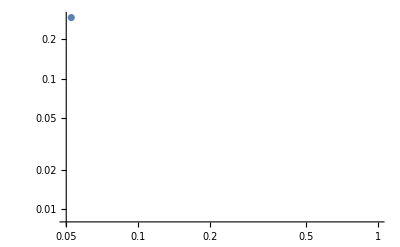

```mathematica
ListLogLogPlot[{pTeta00tb[1]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

```mathematica
ListLogLogPlot[{pTeta00tb[1]},PlotRange->{{0.05,1},{8*10^-3,3*10^-1}}]
```

-Graphics-

```mathematica
pTetaheat=Import["./datafiles/pTetaheat.dat","Data","FieldSeparators"->","];
```

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]]±(pTetaheat[[i]][[2]])/2,pTetaheat[[i]][[3]]±(pTetaheat[[i]][[4]])/2,pTetaheat[[i]][[2n+3]]±(pTetaheat[[i]][[2n+3]])/2},{i,1,Length[pTetaheat]}]
```

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]],pTetaheat[[i]][[3]],pTetaheat[[i]][[2n+3]]},{i,1,Length[pTetaheat]}]
```

```mathematica
pTetatb2[n_]:=Table[{Log10[pTetaheat[[i]][[1]]],pTetaheat[[i]][[3]],pTetaheat[[i]][[2n+1]]},{i,1,Length[pTetaheat]}]
```

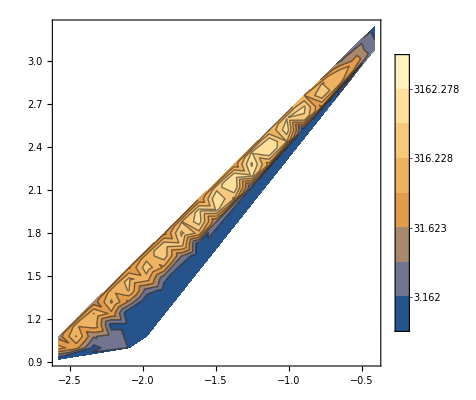

```mathematica
ListContourPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

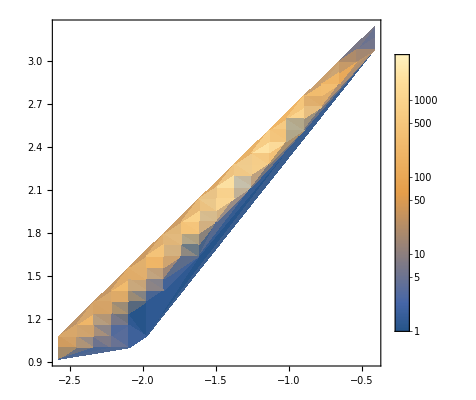

```mathematica
ListDensityPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[pTetatb[1],ScalingFunctions->{"Log10","Log10","Log10"},PlotLegends->Automatic]
```

-Graphics-

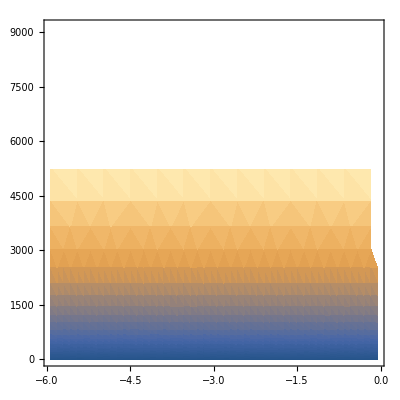

```mathematica
ListDensityPlot[pTetatb2[1]]
```

```mathematica
marker1=Graphics[{or,Disk[]}];
marker2=Graphics[{bl,Disk[]}];
marker3=Graphics[{gr,Disk[]}];
marker4=Graphics[{pur,Disk[]}];
```

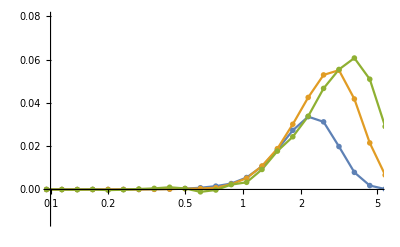

```mathematica
ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},PlotRange->{{0.1,5},{-0.015,0.08}}, PlotMarkers->{marker1,0.021},Joined->True]
```

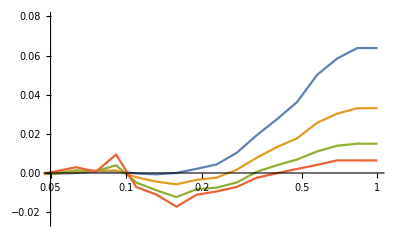

```mathematica
ListLogLinearPlot[{f4tb[1],f4tb[2],f4tb[3],f4tb[4]},PlotRange->{{0.05,1},{-0.025,0.08}},Joined->True]
```

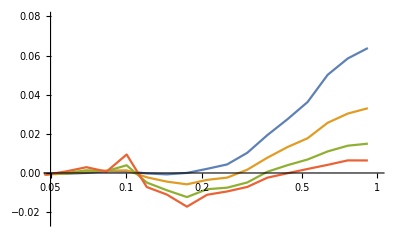

```mathematica
ListLogLinearPlot[{fig4[[;;,{1,3}]],fig4[[;;,{1,5}]],fig4[[;;,{1,7}]],fig4[[;;,{1,9}]]},PlotRange->{{0.05,1},{-0.025,0.08}},Joined->True]
```

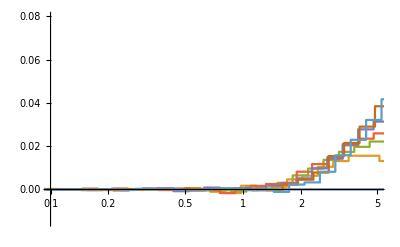

```mathematica
ListLogLinearPlot[{f5tb[1],f5tb[2],f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0]
```

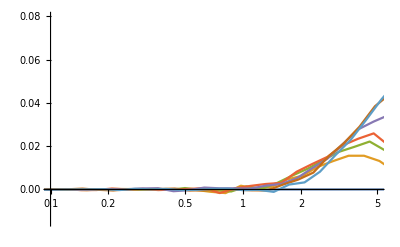

```mathematica
ListLogLinearPlot[{f5tb[1],f5tb[2],f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True]
```

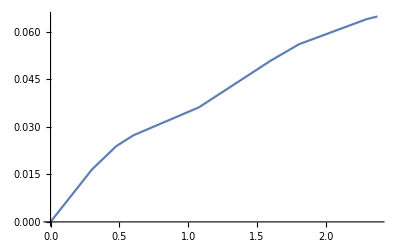

```mathematica
ListPlot[{fig5insert[[;;,{1,2}]]},Joined->True]
```

# Fig 2

```mathematica
dkgr
```

dkgr

```mathematica
sand
```

sand

```mathematica
{RGBColor[233/200,193/200,149/200],Thickness[thsize]}
```

{RGBColor[Rational[233, 200], Rational[193, 200], Rational[149, 200]],Thickness[0.004]}

```mathematica
dkgr={RGBColor[25/255,79/255,93/255],Thickness[thsize]};
ligr={RGBColor[46/255,158/255,144/255],Thickness[thsize]};
ligrr={RGBColor[145/255,177/255,145/255],Thickness[thsize]};
```

```mathematica
sand={RGBColor[233/255,193/255,149/255],Thickness[thsize]};
```

```mathematica
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
skbl={RGBColor[109/250,175/250,237/250],Thickness[thsize]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
re={RGBColor[224/250,31/250,31/250],Thickness[thsize]};
(*lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]};
dkor={RGBColor[227/250,121/250,7/250],Thickness[thsize]};*)
```

```mathematica
or={RGBColor[2,0.1,0],Thickness[thsize]};
dkor={RGBColor[255/255,150/255,113/255],Thickness[thsize]};
lior={RGBColor[255/255,199/255,95/255],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{skbl[[1]],Disk[]}];
marker2=Graphics[{lior[[1]],Disk[]}];
marker3=Graphics[{dkor[[1]],Disk[]}];
marker4=Graphics[{or[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],skbl,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],lior,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],dkor,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],or,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{skbl[[1]],lior[[1]],dkor[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
{RGBColor[227/255,166/255,102/255],Thickness[thsize]}
```

{RGBColor[Rational[227, 255], Rational[166, 255], Rational[2, 5]],Thickness[0.004]}

```mathematica
dkgr={RGBColor[0,37/255,48/255],Thickness[thsize]};
ligr={RGBColor[0,112/255,88/255],Thickness[thsize]};
ligrr={RGBColor[1/255,173/255,158/255],Thickness[thsize]};
```

```mathematica
sand={RGBColor[227/255,166/255,102/255],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

# Fig 3

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{or[[1]],Disk[]}];
marker4=Graphics[{pur[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},PlotRange->{{0.1,6},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,gr,or,pur}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.3],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLinearPlot[{f3tberr[1],f3tberr[2],f3tberr[3]},PlotRange->{{0.2,5.3},{-0.015,0.065}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,gr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.3],0.03,bl,orfill,""MaTeX["p_T \\in 5\\text{-}10\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.0225,gr,blfill,""MaTeX["p_T \\in 10\\text{-}20\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.015,or,blfill,""MaTeX["p_T \\in 20\\text{-}30\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+{}^{197}\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.45],0.053}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.32],0.03±0.002}},{{Log[0.32],0.0225±0.002}},{{Log[0.32],0.015±0.002}},{{Log[Sqrt[5]],-0.01}},{{Log[Sqrt[10]],-0.01}},{{Log[Sqrt[20]],-0.01}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{bl[[1]],gr[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{or[[1]],Disk[]}];
marker4=Graphics[{pur[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f3ReAtb[1],f3ReAtb[2],f3ReAtb[3]},PlotRange->{{0.1,6},{-0.4,2.5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,gr,or,pur}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.3],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLinearPlot[{f3ReAtberr[1],f3ReAtberr[2],f3ReAtberr[3]},PlotRange->{{0.2,5.3},{-0.4,2.5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,gr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.3],1.2,bl,orfill,""MaTeX["p_T \\in 5\\text{-}10\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.95,gr,blfill,""MaTeX["p_T \\in 10\\text{-}20\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],0.7,or,blfill,""MaTeX["p_T \\in 20\\text{-}30\\text{ GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.3],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+{}^{197}\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{-0.6,1.75}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.32],1.2±0.075}},{{Log[0.32],0.95±0.075}},{{Log[0.32],0.7±0.075}},{{Log[Sqrt[5]],-0.01}},{{Log[Sqrt[10]],-0.01}},{{Log[Sqrt[20]],-0.01}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{bl[[1]],gr[[1]],or[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
Sqrt[]
```

Sqrt::argx: Sqrt called with 0 arguments; 1 argument is expected.

Sqrt[]

```mathematica
Sqrt[5]//N
Sqrt[10]//N
Sqrt[20]//N
```

2.23607

3.16228

4.47214

```mathematica
Log[Sqrt[10]]//N
Log[Sqrt[20]]//N
Log[Sqrt[30]]//N
```

1.15129

1.49787

1.7006

```mathematica
test={5,10,20};
```

```mathematica
test[[1]]
```

5

```mathematica
f3tb[n_]:=Join[Table[{Sqrt[test[[n]]](fig3[[i]][[1]]-(fig3[[i]][[2]])/2),fig3[[i]][[2n+1]]},{i,1,Length[fig3]}],{{Sqrt[test[[n]]](fig3[[Length[fig3]]][[1]]+(fig3[[Length[fig3]]][[2]])/2),fig3[[Length[fig3]]][[2n+1]]}}]
```

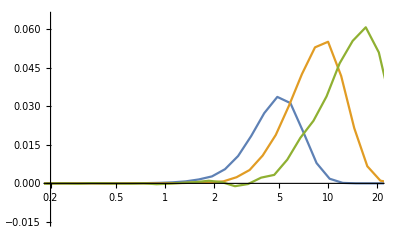

```mathematica
ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},Joined->True,PlotRange->{{0.2,20},{-0.015,0.065}}]
```

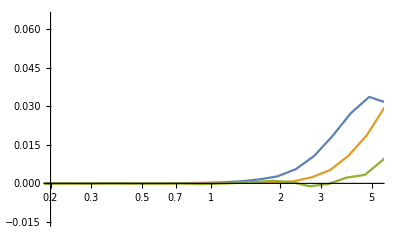

```mathematica
ListLogLinearPlot[{f3tb[1],f3tb[2],f3tb[3]},Joined->True,PlotRange->{{0.2,5.3},{-0.015,0.065}}]
```

# Fig 4

```mathematica
marker1=Graphics[{or[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{bl[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f4tb[1],f4tb[2],f4tb[3],f4tb[4]},PlotRange->{{0.05,1},{-0.025,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{or,gr,pur,bl}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLinearPlot[{f4tberr[1],f4tberr[2],f4tberr[3],f4tberr[4]},PlotRange->{{0.05,1},{-0.025,0.07}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{or,gr,pur,bl}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.08],0.0375,or,orfill,""MaTeX["n=0.5"],Log[3],-Log[0.1],0,0],legbox[Log[0.08],0.03,gr,blfill,""MaTeX["\,n=1"],Log[3],-Log[0.1],0,0],legbox[Log[0.08],0.0225,pur,grfill,""MaTeX["n=1.5"],Log[3],-Log[0.1],0,0],legbox[Log[0.08],0.015,bl,purfill,""MaTeX["\,n=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.08],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+{}^{197}\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.053}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.085],0.0375±0.0025}},{{Log[0.085],0.03±0.0025}},{{Log[0.085],0.0225±0.0025}},{{Log[0.085],0.015±0.0025}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{or[[1]],gr[[1]],pur[[1]],bl[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

# Fig 5

```mathematica
thsize=0.004;
lgy={RGBColor[0.2,0.2,0.2],Thickness[thsize]};
lgyfill=RGBColor[0.85,0.85,0.85];
dgy={RGBColor[0,0,0],Thickness[thsize]};
dgyfill=RGBColor[0.5,0.5,0.5];
gr={RGBColor[0,0.65,0],Thickness[thsize]};
grfill=RGBColor[0.35,1,0.35];
grth={RGBColor[0,0.65,0],Thickness[0.004]};
bl={RGBColor[0,0,1],Thickness[thsize]};
blfill=RGBColor[0.5,0.7,1];
blth={RGBColor[0,0,1],Thickness[0.004]};
or={RGBColor[2,0.1,0],Thickness[thsize]};
orfill=RGBColor[1,0.5,0];
orth={RGBColor[2,0.1,0],Thickness[0.004]};
skbl={RGBColor[109/250,175/250,237/250],Thickness[thsize]};
whfill=RGBColor[1,1,1];
white={RGBColor[1,1,1],Thickness[0.004]};
pur={RGBColor[0.5,0,0.5],Thickness[thsize]};
purfill=RGBColor[1,0.5,1];
mag={RGBColor[1,0,1],Thickness[thsize]};
blor1={RGBColor[0.33,0.033,0.66],Thickness[thsize]};
blor2={RGBColor[0.66,0.066,0.33],Thickness[thsize]};
re={RGBColor[224/250,31/250,31/250],Thickness[thsize]};
lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]}
```

{RGBColor[Rational[24, 25], Rational[167, 250], Rational[13, 50]],Thickness[0.004]}

```mathematica
blor1
```

{RGBColor[0.33, 0.033, 0.66],Thickness[0.004]}

```mathematica
blor2
```

{RGBColor[0.66, 0.066, 0.33],Thickness[0.004]}

```mathematica
skbl
```

{RGBColor[Rational[109, 250], Rational[7, 10], Rational[237, 250]],Thickness[0.004]}

```mathematica
lior,bl,pur,or,gr,skbl
```

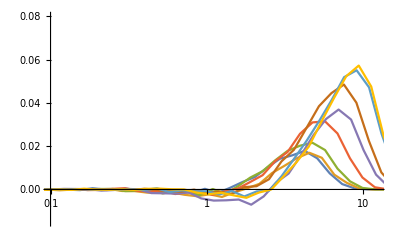

```mathematica
ListLogLinearPlot[{f5tb[2],f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7],f5tb[8],f5tb[9]},PlotRange->{{0.1,238^(1/6)5},{-0.015,0.08}},Joined->True]
```

```mathematica
Alist
```

{1,2.,3.,4.,12.,40.,64.,197.002,238.002}

```mathematica
or={RGBColor[2,0.1,0],Thickness[thsize]};
re={RGBColor[250/250,1/250,1/250],Thickness[thsize]};
(*lior={RGBColor[240/250,167/250,65/250],Thickness[thsize]};
dkor={RGBColor[227/250,121/250,7/250],Thickness[thsize]};*)
dkor={RGBColor[255/255,150/255,113/255],Thickness[thsize]};
lior={RGBColor[255/255,199/255,95/255],Thickness[thsize]};
ye={RGBColor[227/250,200/250,7/250],Thickness[thsize]};
```

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListPlot[{f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7],f5tb[8],f5tb[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListPlot[{f5tberr[3],f5tberr[4],f5tberr[5],f5tberr[6],f5tberr[7],f5tberr[8],f5tberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[1.9],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[2.03],0.07±0.002}},{{Log[2.03],0.063±0.002}},{{Log[2.03],0.056±0.002}},{{Log[2.03],0.049±0.002}},{{Log[2.03],0.042±0.002}},{{Log[2.03],0.035±0.002}},{{Log[2.03],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f5tb[3],f5tb[4],f5tb[5],f5tb[6],f5tb[7],f5tb[8],f5tb[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLinearPlot[{f5tberr[3],f5tberr[4],f5tberr[5],f5tberr[6],f5tberr[7],f5tberr[8],f5tberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[1.9],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[1.9],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[2.03],0.07±0.002}},{{Log[2.03],0.063±0.002}},{{Log[2.03],0.056±0.002}},{{Log[2.03],0.049±0.002}},{{Log[2.03],0.042±0.002}},{{Log[2.03],0.035±0.002}},{{Log[2.03],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f5ReAtb[3],f5ReAtb[4],f5ReAtb[5],f5ReAtb[6],f5ReAtb[7],f5ReAtb[8],f5ReAtb[9]},PlotRange->{{0.1,5},{0.1,3.3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLogPlot[{f5ReAtberr[3],f5ReAtberr[4],f5ReAtberr[5],f5ReAtberr[6],f5ReAtberr[7],f5ReAtberr[8],f5ReAtberr[9]},PlotRange->{{0.1,238^(1/6)*5},{-0.75,3.3}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[2.12],2.8,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],2.5,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],2.2,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.9,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.6,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.3,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[2.12],1.0,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],4}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{0.1,4}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,4},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,4},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,4},{-1,0}] }]];
legend=ListPlot[{{{Log[2.25],2.8±0.1}},{{Log[2.25],2.5±0.1}},{{Log[2.25],2.2±0.1}},{{Log[2.25],1.9±0.1}},{{Log[2.25],1.6±0.1}},{{Log[2.25],1.3±0.1}},{{Log[2.25],1.0±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
f5tb2[n_]:=Join[Table[{(fig5[[i]][[1]]-(fig5[[i]][[2]])/2),fig5[[i]][[2n+1]]},{i,1,Length[fig5]}],{{(fig5[[Length[fig5]]][[1]]+(fig5[[Length[fig5]]][[2]])/2),fig5[[Length[fig5]]][[2n+1]]}}]
f5tberr2[n_]:=Table[{fig5[[i]][[1]],fig5[[i]][[2n+1]]±fig5[[i]][[2n+2]]},{i,1,Length[fig5]}]
```

```mathematica
marker1=Graphics[{bl[[1]],Disk[]}];
marker2=Graphics[{skbl[[1]],Disk[]}];
marker3=Graphics[{pur[[1]],Disk[]}];
marker4=Graphics[{gr[[1]],Disk[]}];
marker5=Graphics[{lior[[1]],Disk[]}];
marker6=Graphics[{dkor[[1]],Disk[]}];
marker7=Graphics[{re[[1]],Disk[]}];
predictionplot=ListLogLinearPlot[{f5tb2[3],f5tb2[4],f5tb2[5],f5tb2[6],f5tb2[7],f5tb2[8],f5tb2[9]},PlotRange->{{0.1,5},{-0.015,0.08}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["A^{1/6}R_L\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.07],0.06}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];

predictionplot2=ListLogLinearPlot[{f5tberr2[3],f5tberr2[4],f5tberr2[5],f5tberr2[6],f5tberr2[7],f5tberr2[8],f5tberr2[9]},PlotRange->{{0.1,5},{-0.015,0.08}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021},{marker5,0.021},{marker6,0.021},{marker7,0.021}},Frame->True, FrameStyle->Directive[Black,20],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}\\text{ Ratio}",Magnification->1.5*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta\\sqrt{p_T}"],FontFamily->"Latin Modern Roman",Magnification->1.5*magl],None}},PlotStyle->{bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.15],0.07,bl,orfill,""MaTeX["e+{}^3\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.063,skbl,blfill,""MaTeX["e+{}^4\\text{He}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.056,pur,grfill,""MaTeX["e+{}^{12}\\text{C}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.049,gr,purfill,""MaTeX["e+{}^{40}\\text{Ca}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.042,lior,blfill,""MaTeX["e+{}^{64}\\text{Cu}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.035,dkor,blfill,""MaTeX["e+{}^{197}\\text{Au}"],Log[3],-Log[0.1],0,0],legbox[Log[0.15],0.028,re,blfill,""MaTeX["e+{}^{238}\\text{U}"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.16],0.07±0.002}},{{Log[0.16],0.063±0.002}},{{Log[0.16],0.056±0.002}},{{Log[0.16],0.049±0.002}},{{Log[0.16],0.042±0.002}},{{Log[0.16],0.035±0.002}},{{Log[0.16],0.028±0.002}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026},{marker5,0.026},{marker6,0.026},{marker7,0.026}},IntervalMarkersStyle->{bl[[1]],skbl[[1]],pur[[1]],gr[[1]],lior[[1]],dkor[[1]],re[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
LinearModelFit[fig5insert,x,x]
```

FittedModel[0.00713348+0.0230583 x]

```mathematica
Log[y]=number Log[A]
```

Set::write: Tag Log in Log[y] is Protected.

number Log[A]

```mathematica
Exit[]
```

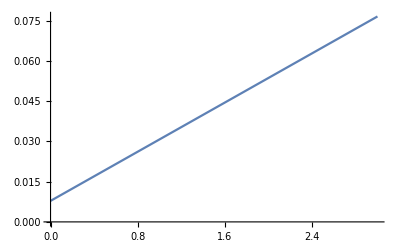

```mathematica
Plot[0.022907x+0.007828,{x,0,3}]
```

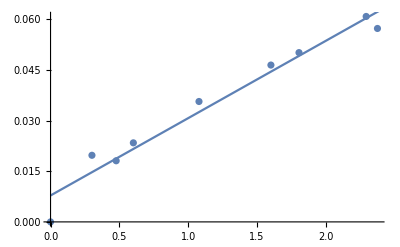

```mathematica
Show[ListPlot[fig5insert],Plot[0.022907x+0.007828,{x,0,3}]]
```

```mathematica
fig5insert
```

```mathematica
Table[{{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]}},{i,2,Length[fig5insert]}]//StandardForm
```

{{{0.30103,-1.78216}},{{0.477121,-1.62236}},{{0.60206,-1.56406}},{{1.07918,-1.44219}},{{1.60206,-1.29358}},{{1.80618,-1.25181}},{{2.29447,-1.19479}},{{2.37658,-1.18871}}}

```mathematica
Table[{{fig5insert[[i]][[1]],fig5insert[[i]][[2]]}},{i,3,Length[fig5insert]}]//StandardForm
```

{{{0.477121,0.0181179}},{{0.60206,0.0234332}},{{1.07918,0.0343877}},{{1.60206,0.0399072}},{{1.80618,0.0507151}},{{2.29447,0.059843}},{{2.37658,0.06106}}}

```mathematica
Table[{{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]}},{i,3,Length[fig5insert]}]//StandardForm
```

{{{0.477121,-1.74189}},{{0.60206,-1.63017}},{{1.07918,-1.4636}},{{1.60206,-1.39895}},{{1.80618,-1.29486}},{{2.29447,-1.22299}},{{2.37658,-1.21424}}}

```mathematica
fig5insertlist={{{0.30103,-1.7821608692210524}},{{0.477121,-1.622355043905958}},{{0.60206,-1.5640617168455602}},{{1.07918,-1.4421933464363175}},{{1.60206,-1.2935792435337619}},{{1.80618,-1.2518142995776131}},{{2.29447,-1.1947942088868977}},{{2.37658,-1.18870858448702}}};
```

```mathematica
fig5insertlist={{{0.30103,-1.704615452029604}},{{0.477121,-1.7418921417179711}},{{0.60206,-1.6301684007992265}},{{1.07918,-1.463596870723851}},{{1.60206,-1.3989487424542169}},{{1.80618,-1.2948627138361388}},{{2.29447,-1.222986642904497}},{{2.37658,-1.2142432000373569}}}
```

{{{0.30103,-1.70462}},{{0.477121,-1.74189}},{{0.60206,-1.63017}},{{1.07918,-1.4636}},{{1.60206,-1.39895}},{{1.80618,-1.29486}},{{2.29447,-1.22299}},{{2.37658,-1.21424}}}

```mathematica
Log10[3]//N
```

0.477121

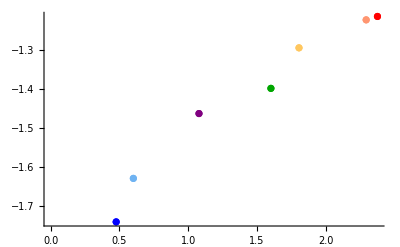

```mathematica
ListPlot[fig5insertlist,PlotStyle->{White,bl,skbl,pur,gr,lior,dkor,re}]
```

```mathematica
LinearModelFit[Table[{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]},{i,2,Length[fig5insert]}],x,x]
```

FittedModel[-1.76182+0.261411 x]

```mathematica
10^-1.79442
```

0.0160539

```mathematica
0.0161
```

```mathematica
Log10[peak]=-1.79442+0.254687 Log10[A]
```

```mathematica
Log[4]//N
```

1.38629

```mathematica
Alist
```

{1,2.,3.,4.,12.,40.,64.,197.002,238.002}

```mathematica
10^-1.76182
```

0.0173053

```mathematica
fig
```

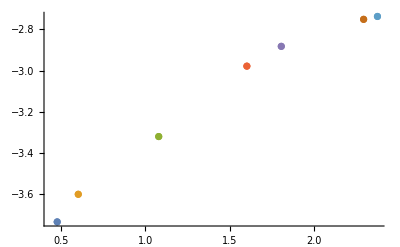

```mathematica
ListPlot[Table[{{fig5insert[[i]][[1]],Log[fig5insert[[i]][[2]]]}},{i,3,Length[fig5insert]}]]
```

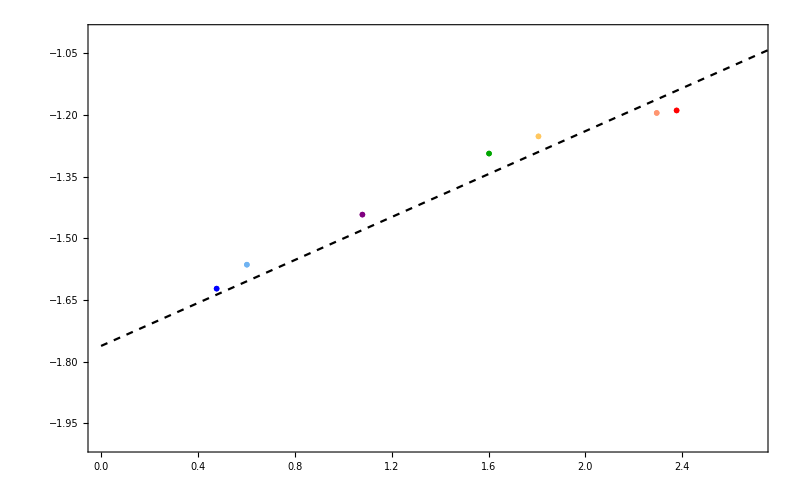

```mathematica
predictionplot2=ListPlot[fig5insertlist,PlotRange->{{0,2.7},{-1.0,-2}}, PlotMarkers->{{marker0,0.05},{marker1,0.05},{marker2,0.05},{marker3,0.05},{marker4,0.05},{marker5,0.05},{marker6,0.05},{marker7,0.05}},Joined->True,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\log(\\text{Peak Value})",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\log A"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{White,bl,skbl,pur,gr,lior,dkor,re}, PlotRange->All, ImageSize->800,Epilog->Join[{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\frac{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{Au}}-\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}{\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle_{e+\\text{p}}}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.11],0.53}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot=ListPlot[Table[{fig5insert[[i]][[1]],Log10[fig5insert[[i]][[2]]]},{i,3,Length[fig5insert]}],Joined->True,PlotStyle->{Dashed,Black}];
predictionplot=Plot[-1.7618246920348026+0.26141129268304425 x,{x,0,3},PlotStyle->{Dashed,Black}];
Show[predictionplot2,predictionplot]
```

# Supplemental

## pT-eta dependence

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{f2tb[1],f2tb[2],f2tb[3],f2tb[4]},PlotRange->{{0.05,1},{0.5*10^-1,3}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{f2tberr[1],f2tberr[2],f2tberr[3],f2tberr[4]},PlotRange->{{0.05,1},{3*10^-1,5}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.03],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.023],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0175],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.0135],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.9]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.22],Log[3.2]}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.03]±0.1}},{{Log[0.405],Log[0.023]±0.1}},{{Log[0.405],Log[0.0175]±0.1}},{{Log[0.405],Log[0.0135]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta00tb[1],pTeta00tb[2],pTeta00tb[3],pTeta00tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta00tberr[1],pTeta00tberr[2],pTeta00tberr[3],pTeta00tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta10tb[1],pTeta10tb[2],pTeta10tb[3],pTeta10tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta10tberr[1],pTeta10tberr[2],pTeta10tberr[3],pTeta10tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta11tb[1],pTeta11tb[2],pTeta11tb[3],pTeta11tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta11tberr[1],pTeta11tberr[2],pTeta11tberr[3],pTeta11tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta12tb[1],pTeta12tb[2],pTeta12tb[3],pTeta12tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta12tberr[1],pTeta12tberr[2],pTeta12tberr[3],pTeta12tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta20tb[1],pTeta20tb[2],pTeta20tb[3],pTeta20tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta20tberr[1],pTeta20tberr[2],pTeta20tberr[3],pTeta20tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta21tb[1],pTeta21tb[2],pTeta21tb[3],pTeta21tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta21tberr[1],pTeta21tberr[2],pTeta21tberr[3],pTeta21tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{ligrr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{pTeta22tb[1],pTeta22tb[2],pTeta22tb[3],pTeta22tb[4]},PlotRange->{{0.05,1},{0.3*10^-1,5}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],dkgr,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{pTeta22tberr[1],pTeta22tberr[2],pTeta22tberr[3],pTeta22tberr[4]},PlotRange->{{0.05,1},{0.3*10^-1,6}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,ligrr,ligr,dkgr}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.34],Log[0.3],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.2],ligrr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.135],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.34],Log[0.093],dkgr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{ }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}},{{Log[0.405],Log[0.009]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026},{marker4,0.026}},IntervalMarkersStyle->{sand[[1]],ligrr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

## K=0 comparison

```mathematica
marker1=Graphics[{sand[[1]],Disk[]}];
marker2=Graphics[{gr[[1]],Disk[]}];
marker3=Graphics[{ligr[[1]],Disk[]}];
marker4=Graphics[{dkgr[[1]],Disk[]}];
predictionplot=ListLogLogPlot[{baselinetb[1],baselinetb[2],baselinetb[3]},PlotRange->{{0.05,0.999},{1*10^-3,3*10^-1}},Joined->True,InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{sand,gr,ligr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],sand,orfill,""MaTeX["e+\\text{p, }"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],gr,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],ligr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\text{Two-Point Energy Correlator}"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.15],Log[0.2]}],Text[Style[MaTeX["\\langle \\mathcal{E}^{n}\\mathcal{E}^{n}\\rangle"],FontFamily->"Latin Modern Roman",Magnification->1.25magl],{Log[0.14],Log[0.14]}],Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
predictionplot2=ListLogLogPlot[{baselinetberr[1],baselinetberr[2],baselinetberr[3]},PlotRange->{{0.05,1},{4*10^-3,1.5*10^-1}}, PlotMarkers->{{marker1,0.021},{marker2,0.021},{marker3,0.021},{marker4,0.021}},Frame->True, FrameStyle->Directive[Black,24],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.75*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["\\theta"],FontFamily->"Latin Modern Roman",Magnification->1.75*magl],None}},PlotStyle->{sand,gr,ligr,or}, PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.38],Log[0.028],sand,orfill,""MaTeX["\, e+\\text{p }"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.019],gr,blfill,""MaTeX["e+{}^{2}\\text{D, }K=0"],Log[3],-Log[0.1],0,0],legbox[Log[0.38],Log[0.013],ligr,blfill,""MaTeX["e+{}^{197}\\text{Au, }K=0"],Log[3],-Log[0.1],0,0],{Text[Style[MaTeX["\\sqrt{s}=7 \\text{ TeV}, \\, p_T=500\\text{-}550\\text{ GeV} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.5,0.68},{-1,0}] ,Text[Style[MaTeX[" R=0.5, \\,  |\\eta|<1.9, \\, \\text{anti-}\\mathrm{k_T} "],FontFamily->"Latin Modern Roman",Magnification->0.75*magl],{-3.25,0.53},{-1,0}],Text[Style[MaTeX["\\text{CMS Open Data} "],Magnification->magl],{-3.41,0.38},{-1,0}] }]];
legend=ListPlot[{{{Log[0.405],Log[0.028]±0.1}},{{Log[0.405],Log[0.019]±0.1}},{{Log[0.405],Log[0.013]±0.1}}},ImageSize->500, PlotMarkers->{{marker1,0.026},{marker2,0.026},{marker3,0.026}},IntervalMarkersStyle->{sand[[1]],gr[[1]],ligr[[1]],dkgr[[1]]}];
Show[predictionplot2,predictionplot,legend]
```

-Graphics-

## qhat

```mathematica
ListPlot3D[qhatxQdata,ScalingFunctions->{"Log10","Log10","Log10"}]
```

-Graphics3D-

```mathematica
Table[i,{i,0,0.42,0.42/6}]
```

{0.,0.07,0.14,0.21,0.28,0.35,0.42}

```mathematica
qhatxQK2=Import["./datafiles/qhat_data_Au_K2.dat","Data","FieldSeparators"->","];
qhatxQK4=Import["./datafiles/qhat_data_Au_K4.dat","Data","FieldSeparators"->","];
qhatxQK10=Import["./datafiles/qhat_data_Au_K10.dat","Data","FieldSeparators"->","];
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK2=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK2[[i]][[j]]=="nan",0,qhatxQK2[[i]][[j]]]},{i,5,Length[qhatxQK2]},{j,1,Length[qhatxQK2[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK4=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK4[[i]][[j]]=="nan",0,qhatxQK4[[i]][[j]]]},{i,5,Length[qhatxQK4]},{j,1,Length[qhatxQK4[[5]]]}],1],Abs[#[[3]]]>0&];
qhatxQdataK10=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQK10[[i]][[j]]=="nan",0,qhatxQK10[[i]][[j]]]},{i,5,Length[qhatxQK10]},{j,1,Length[qhatxQK10[[5]]]}],1],Abs[#[[3]]]>0&];
```

```mathematica
xQcoord=Table[{10^i,10^j},{j,-3,0,(0-(-3))/20},{i,0,3,(3-0)/20}];
qhatxQdata=Select[Flatten[Table[{xQcoord[[i-4]][[j]][[2]],xQcoord[[i-4]][[j]][[1]],If[qhatxQ[[i]][[j]]=="nan",0,qhatxQ[[i]][[j]]]},{i,5,Length[qhatxQ]},{j,1,Length[qhatxQ[[5]]]}],1],Abs[#[[3]]]>0&];
```

```mathematica
ListContourPlot[qhatxQdataK2, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]

ListContourPlot[qhatxQdataK4, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]

ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,0.90}},44,LegendMarkerSize->{20,605}],ColorFunction->(ColorData["BlueGreenYellow",Rescale[#,{0,0.90}]]&),ColorFunctionScaling->False,(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->{{0.001,1},{1,1000},{0,0.90}}, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
Max[Table[qhatxQdataK10[[i]][[3]],{i,1,Length[qhatxQdataK10]}]]
```

0.903

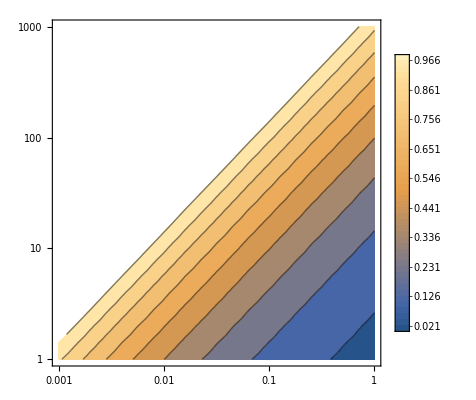

```mathematica
ListContourPlot[qhatxQdataK10, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{0,1}},46,LegendMarkerSize->{20,605}]]
```

```mathematica
PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData["SunsetColors",Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,
```

```mathematica
BarLegend[{"BlueGreenYellow",{0,0.90}},Ticks->Table[i,{i,0,0.90,0.90/6}],LegendMarkerSize->{20,605}]//StandardForm
```

```mathematica
ListContourPlot[qhatxQdata, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,0.48}},Ticks->Table[i,{i,0,0.48,0.48/6}],LegendMarkerSize->{20,605}],(*PlotLegends->{0,0.06,0.12,0.18,0.24,0.30,0.36,0.42},*)
FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[qhatxQdata, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Log10"},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},ColorFunction->"DeepSeaColors",
FrameLabel->{{Style[MaTeX["\\mathrm{Q^2[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotRange->All, ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
TicksStyle->Large,
```

```mathematica
ColorFunction->"SunsetColors","BlueGreenYellow",DeepSeaColors,
```

-Graphics-

## pT eta heat

```mathematica
pTetatb[n_]:=Table[{pTetaheat[[i]][[1]]+(pTetaheat[[i]][[2]])/2,pTetaheat[[i]][[3]]+(pTetaheat[[i]][[4]])/2,pTetaheat[[i]][[2n+3]]+0.1},{i,1,Length[pTetaheat]}]
```

```mathematica
BarLegend[{{"SunsetColors","Reverse"},{0,6}},Ticks->Table[i,{i,0,6,6/6}],LegendMarkerSize->{20,605}]
```

```mathematica
BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11]
```

```mathematica
Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},
FrameLabel->{{Style[MaTeX["\\mathrm{E^nE^n}~\\mathrm{Correlator}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["R_L"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},PlotStyle->{skbl,lior,dkor,or}, PlotRange->All,
```

```mathematica
ListDensityPlot[pTetatb[1]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[4]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[5]/. {x_,y_,z_}->{x,y,Log10[z]},  InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[6]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[7]/. {x_,y_,z_}->{x,y,Log10[z]},  InterpolationOrder->0,Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[8]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

```mathematica
ListDensityPlot[pTetatb[9]/. {x_,y_,z_}->{x,y,Log10[z]}, InterpolationOrder->0, Frame->True, FrameStyle->Directive[Black,18],Axes->{True,False},ScalingFunctions->{"Log10","Log10","Linear"},PlotRange->{{0.0005,0.86},{2,2000},{Log10[0.1],Log10[1000000]}},FrameTicks->{{{1,10,100,1000},None},{{0.001,0.01,0.1,1},None}},PlotLegends->BarLegend[{Automatic,{Log10[1],Log10[1000000]}},11],ColorFunction->(ColorData[{"SunsetColors","Reverse"},Rescale[#,{Log10[0.1],Log10[1000000]}]]&),ColorFunctionScaling->False,FrameLabel->{{Style[MaTeX["Q^2\\mathrm{[GeV]}",Magnification->1.25*magl],FontFamily->"Latin Modern Roman"],None},
{Style[MaTeX["x_B"],FontFamily->"Latin Modern Roman",Magnification->1.25*magl],None}},ImageSize->800,Epilog->Join[
legbox[Log[0.4],Log[0.03],or,orfill,""MaTeX["p_T = 5-10\\text{GeV}"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.023],bl,blfill,""MaTeX["e+\\text{Au, }K=2"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0175],gr,blfill,""MaTeX["e+\\text{Au, }K=4"],Log[3],-Log[0.1],0,0],legbox[Log[0.4],Log[0.0135],pur,blfill,""MaTeX["e+\\text{Au, }K=10"],Log[3],-Log[0.1],0,0]]]
```

-Graphics-

# NP

```mathematica
f2tbtemp[n_]:=Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[1]]-(fig2[[i]][[2]])/2)},{i,1,Length[fig2]}]
```

```mathematica
rr=1;
JqLONLL[2][20,θ^2/4,20];
```

```mathematica
NIntegrate[θ D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.5,1}]
```

NIntegrate::inumr: The integrand θ JqLONLL[2]^(0,1,0)[20,θ^2/4,20] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate[θ ∂_z JqLONLL[2][20,z,20]/.{z→θ^2/4},{θ,0.5,1}]

```mathematica
LogLinearPlot[θ/0.206284 D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.01,1},PlotRange->{{0.05,1},{0,5}},PlotStyle->Red]
```

-Graphics-

```mathematica
1/20//N
```

0.05

```mathematica
NIntegrate[Interpolation[f2tbtemp[1]][x],{x,0.5,1}]
```

InterpolatingFunction::dmvali: The integration endpoint 1 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0426119

```mathematica
NIntegrate[θ (D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ),{θ,0.5,1}]
```

NIntegrate::inumr: The integrand 1/(5 θ)+θ JqLONLL[2]^(0,1,0)[20,θ^2/4,20] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate[θ (∂_z JqLONLL[2][20,z,20]/.{z→θ^2/4})+4/(20 θ),{θ,0.5,1}]

```mathematica
LogLinearPlot[1/0.344913(θ (D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0,5}},PlotStyle->{Green}]
```

-Graphics-

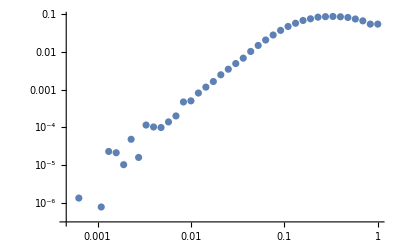

```mathematica
ListLogLogPlot[{pTeta22tb[1]}]
```

```mathematica
f2tbtemp[n_]:=Table[{fig2[[i]][[1]]-(fig2[[i]][[2]])/2,(fig2[[i]][[2n+1]])/(fig2[[i]][[1]]-(fig2[[i]][[2]])/2)},{i,1,Length[fig2]}]
```

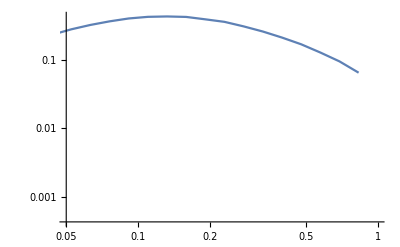

```mathematica
ListLogLogPlot[f2tbtemp[1],Joined->True,PlotRange->{{0.05,1},All}]
```

```mathematica
LogLogPlot[1/5 D[JqLONLL[2][20,z,20],z]/.{z->θ^2/4},{θ,0.01,1},PlotRange->{{0.05,1},{0.00001,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
α[θ 20]/α[20]
```

α[20 θ]/α[20]

```mathematica
gTqq0[2]
```

gTqq0[2]

```mathematica
pTeta20tbtemp[n_]:=Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2)},{i,1,Length[pTeta20]}]
```

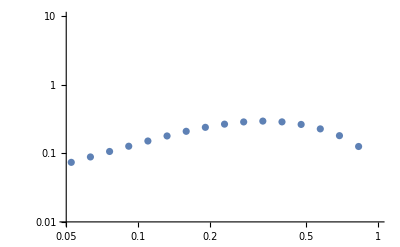

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4 θ( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/8 θ(1/5( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+4/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

```mathematica
pTeta20tbtemp[n_]:=Table[{pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2,(pTeta20[[i]][[2n+1]])/(pTeta20[[i]][[1]]-(pTeta20[[i]][[2]])/2)},{i,1,Length[pTeta20]}]
pTeta21tbtemp[n_]:=Table[{pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2,(pTeta21[[i]][[2n+1]])/(pTeta21[[i]][[1]]-(pTeta21[[i]][[2]])/2)},{i,1,Length[pTeta21]}]
pTeta22tbtemp[n_]:=Table[{pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2,(pTeta22[[i]][[2n+1]])/(pTeta22[[i]][[1]]-(pTeta22[[i]][[2]])/2)},{i,1,Length[pTeta22]}]
```

```mathematica
LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
Cosh[-Log[Tan[θ/2]]]
```

1/2 Cot[θ/2] (1+Tan[θ/2]^2)

```mathematica
LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/20 Cosh[-Log[Tan[θ/2]]]),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
Cosh[-Log[Tan[θ/2]]]
```

1/2 Cot[θ/2] (1+Tan[θ/2]^2)

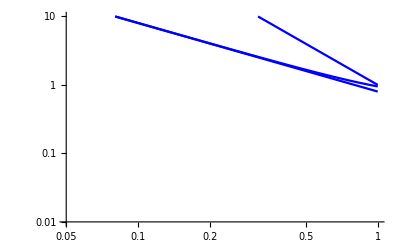

```mathematica
LogLogPlot[{4/5 Cosh[-Log[Tan[θ/2]]],4/(5 θ),1/θ^2},{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

```mathematica
(D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})/.{θ->1}
```

JqLONLL[2]^(0,1,0)[5,1/4,5]+JqNLONLL[2]^(0,1,0)[5,1/4,5]

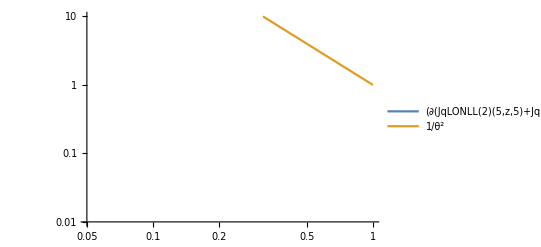

```mathematica
LogLogPlot[{(D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4}),1/θ^2},{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotLegends->"Expressions"]
```

```mathematica
Show[LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[(1/4( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue],LogLogPlot[(1/4( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Green]]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/7((D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+(2π 0.31)/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

-Graphics-

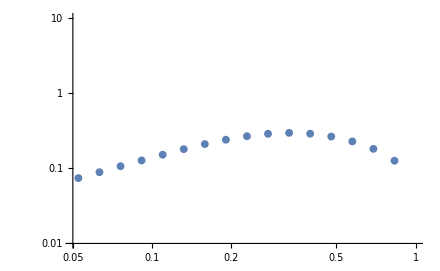

```mathematica
Show[ListLogLogPlot[pTeta20tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/5},{}}],LogLogPlot[(1/4( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/8(1/5( D[JqLONLL[2][5,z,5]+JqNLONLL[2][5,z,5],z]/.{z->θ^2/4})+4/(5 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

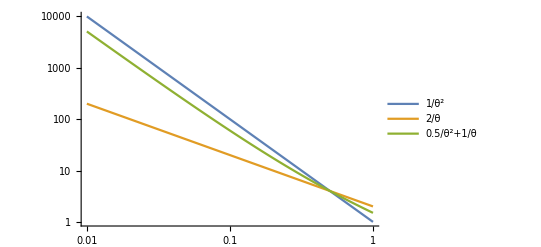

```mathematica
LogLogPlot[{1/θ^2,2/θ,0.5/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

```mathematica
Log[Exp[x^-2]]
```

Log[ⅇ^(1/x^2)]

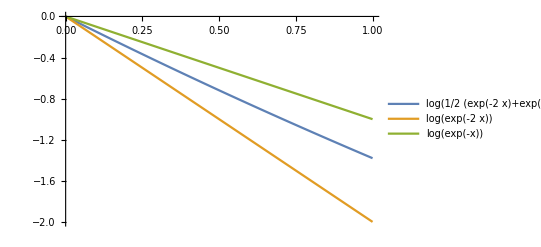

```mathematica
Plot[{Log[(Exp[-2x]+Exp[-x])/2],Log[Exp[-2x]],Log[Exp[-x]]},{x,0,1},PlotLegends->"Expressions"]
```

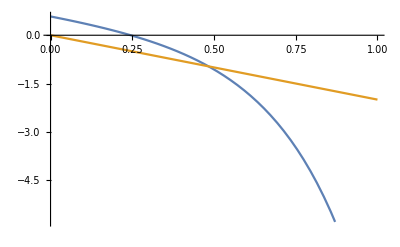

```mathematica
Plot[{-2x+Exp[x]-1/2 Exp[2x]+1/3 Exp[3x]-1/4 Exp[4x],-2x},{x,0,1}]
```

```mathematica
Log[]
```

Log::argt: Log called with 0 arguments; 1 or 2 arguments are expected.

Log[]

```mathematica
Series[Log[a/θ^2+b/θ],{θ,0,4}]
```

Log[a/θ^2]+(b θ)/a-(b^2 θ^2)/(2 a^2)+(b^3 θ^3)/(3 a^3)-(b^4 θ^4)/(4 a^4)+O[θ]^5

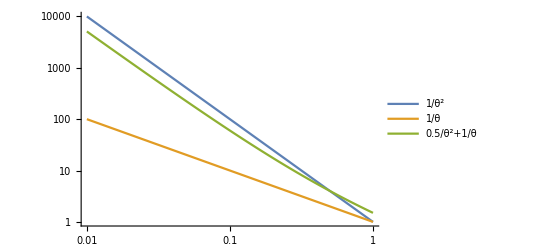

```mathematica
LogLogPlot[{1/θ^2,1/θ,0.5/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

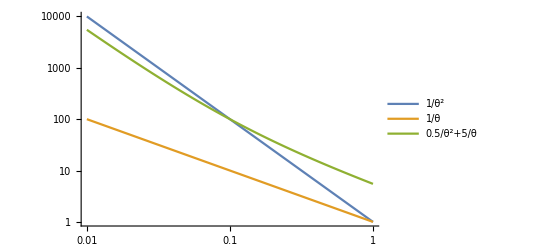

```mathematica
LogLogPlot[{1/θ^2,1/θ,0.5/θ^2+5/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

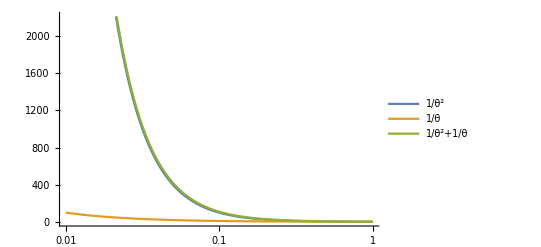

```mathematica
LogLinearPlot[{1/θ^2,1/θ,1/θ^2+1/θ},{θ,0.01,1},PlotLegends->"Expressions"]
```

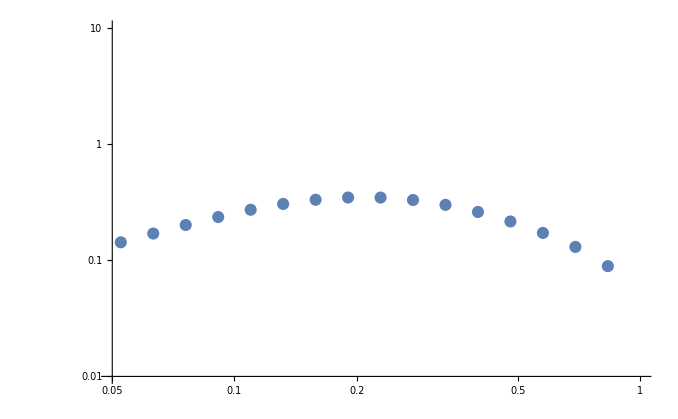

```mathematica
Show[ListLogLogPlot[pTeta21tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/10},{}}],LogLogPlot[(1/5( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/6(1/5( D[JqLONLL[2][10,z,10]+JqNLONLL[2][10,z,10],z]/.{z->θ^2/4})+4/(10θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

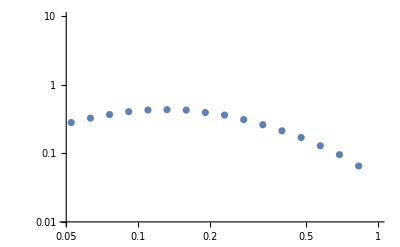

```mathematica
Show[ListLogLogPlot[pTeta22tbtemp[1],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/20},{}}],LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red],LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]]
```

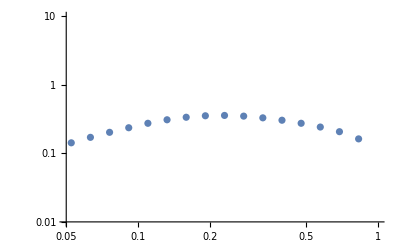

```mathematica
ListLogLogPlot[pTeta21tbtemp[2],PlotRange->{{0.05,1},{0.01,10}},GridLines->{{1/10},{}}]
```

```mathematica
LogLogPlot[1/2(1/5( D[JqLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+1/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.00001,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
LogLogPlot[(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Red]
```

-Graphics-

```mathematica
LogLogPlot[1/4(1/5( D[JqLONLL[2][20,z,20]+JqNLONLL[2][20,z,20],z]/.{z->θ^2/4})+4/(20 θ)),{θ,0.01,1},PlotRange->{{0.05,1},{0.01,10}},PlotStyle->Blue]
```

-Graphics-

```mathematica
ListLogLogPlot[f2tbtemp[1],PlotRange->{{0.05,1},{0.01,10}}]
```

-Graphics-

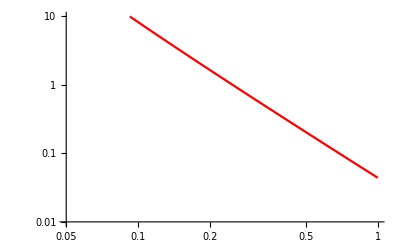
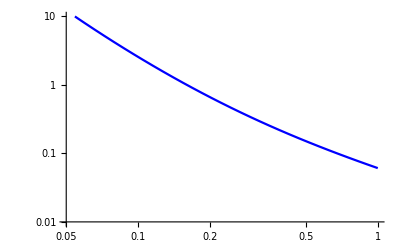
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

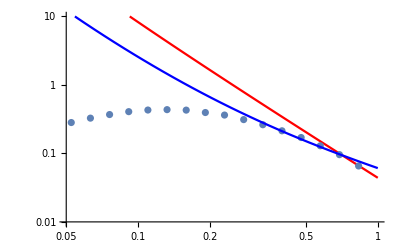

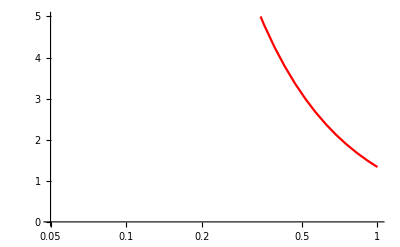
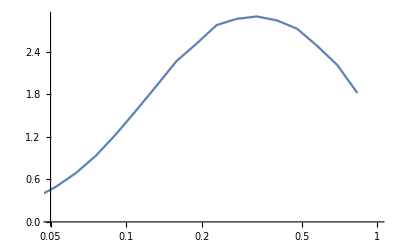
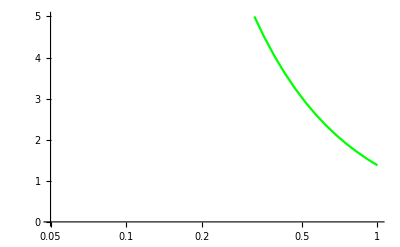
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

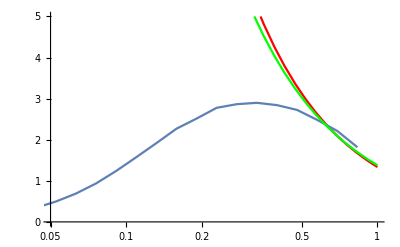

```mathematica
HEX/RGB
#002530/rgb(0,37,48)
#007058/rgb(0,112,88)
#01ad9e/rgb(1/255,173/255,158/255)
#e3a666/rgb(227/255,166/255,102/255)
```

HEX/RGB